```mathematica
PlotsPath = "/Users/brunogoes/Dropbox/00--Thesis/Figures/Chap6/";
overleafPath ="/Users/brunogoes/Dropbox/Aplicativos/Overleaf/000Goes-Bruno-PhDThesis/Figures/Chap6/";
fontsize = 24;
alphabetlabel={"(a)","(b)","(c)","(d)","(e)","(f)","(g)","(h)","(i)","(j)","(k)","(l)","(m)","(n)","(o)","(p)","(q)","(r)","(s)","(t)","(u)","(v)","(w)","(x)","(y)","(z)"};
ClearAll[MPLColorMap]
<<"http://pastebin.com/raw/pFsb4ZBS";
MPLColorMap["Inferno"];
```

# Chapter 6: SPI subjected to a in-plane magnetic field

## Author: Bruno Ortega Goes

## Parameters set definitions and loading experimental data/simulations☑

```mathematica
(*All the physical parameter are real*)
$Assumptions =
 {nx^2+ny^2+nz^2 == 1 &&
  Ωg>0 &&
  Ωe>0 &&
  ΩR>0 &&
  ΩL>0 &&
 γ>0 &&
 Γ>0};
```

#### 2) Exporting experimental data

It is necessary to change the path of the experimental data in your notebook if you want the program to run!

```mathematica
PrettyTiming[data150=Import["/Users/brunogoes/Dropbox/01-Work/22--SPIMagneticField/ExperimentalData/Data/Data_150mT.csv"];data250=Import["/Users/brunogoes/Dropbox/01-Work/22--SPIMagneticField/ExperimentalData/Data/Data_250mT.csv"];data350=Import["/Users/brunogoes/Dropbox/01-Work/22--SPIMagneticField/ExperimentalData/Data/Data_350mT.csv"];data450=Import["/Users/brunogoes/Dropbox/01-Work/22--SPIMagneticField/ExperimentalData/Data/Data_450mT.csv"];]
dataexp1list={data150,data250,data350,data450};
```

0h : 0m : 0s

```mathematica
PrettyTiming[data150dcp=Import["/Users/brunogoes/Dropbox/01-Work/22--SPIMagneticField/ExperimentalData/DataFig2c/Data_150mT_dcp.csv"];data250dcp=Import["/Users/brunogoes/Dropbox/01-Work/22--SPIMagneticField/ExperimentalData/DataFig2c/Data_250mT_dcp.csv"];data350dcp=Import["/Users/brunogoes/Dropbox/01-Work/22--SPIMagneticField/ExperimentalData/DataFig2c/Data_350mT_dcp.csv"];data450dcp=Import["/Users/brunogoes/Dropbox/01-Work/22--SPIMagneticField/ExperimentalData/DataFig2c/Data_450mT_dcp.csv"];]
datadcplist={data150dcp,data250dcp,data350dcp,data450dcp};
```

0h : 0m : 0s

```mathematica
PrettyTiming[data0g2=Import["/Users/brunogoes/Dropbox/01-Work/22--SPIMagneticField/ExperimentalData/Datag2/Data_0mT.csv"];data20g2=Import["/Users/brunogoes/Dropbox/01-Work/22--SPIMagneticField/ExperimentalData/Datag2/Data_20mT.csv"];data40g2=Import["/Users/brunogoes/Dropbox/01-Work/22--SPIMagneticField/ExperimentalData/Datag2/Data_40mT.csv"];data60g2=Import["/Users/brunogoes/Dropbox/01-Work/22--SPIMagneticField/ExperimentalData/Datag2/Data_60mT.csv"];data90g2=Import["/Users/brunogoes/Dropbox/01-Work/22--SPIMagneticField/ExperimentalData/Datag2/Data_90mT.csv"];data100g2=Import["/Users/brunogoes/Dropbox/01-Work/22--SPIMagneticField/ExperimentalData/Datag2/Data_100mT.csv"];data120g2=Import["/Users/brunogoes/Dropbox/01-Work/22--SPIMagneticField/ExperimentalData/Datag2/Data_120mT.csv"];data180g2=Import["/Users/brunogoes/Dropbox/01-Work/22--SPIMagneticField/ExperimentalData/Datag2/Data_180mT.csv"];]
datag2list={data0g2,data20g2,data40g2,data60g2,data90g2,data100g2,data120g2,data180g2};
```

0h : 0m : 0s

#### 3) Parameters Exp.1: Probing the dynamics and coherence of a semiconductor hole spin via acoustic phonon-assisted excitation

```mathematica
Clear[Experimentalγ,ExperimentalΩe,ExperimentalΩg]
τtrion=450;(*This is constant because it depends solely on the cavity used in the experiment*)

Experimentalγ[τtrion_]:= 1/τtrion;(*ps^-1*)
ExperimentalΩe[B_]:=((0.38*58)/658)B(*ps^-1*);
ExperimentalΩg[B_]:=((0.38*58)/658)B(*ps^-1*);

(*The following experimental physical parameters follow Ref. https://arxiv.org/pdf/2207.05981.pdf*)
PhysicalParameters0   = {Ωe->ExperimentalΩe[0.0]/Experimentalγ[τtrion],Ωg->ExperimentalΩg[0.0]/Experimentalγ[τtrion],γ->1.};
PhysicalParameters30  = {Ωe->ExperimentalΩe[0.03]/Experimentalγ[τtrion],Ωg->ExperimentalΩg[0.03]/Experimentalγ[τtrion],γ->1.};
PhysicalParameters150 = {Ωe->ExperimentalΩe[0.15]/Experimentalγ[τtrion],Ωg->ExperimentalΩg[0.15]/Experimentalγ[τtrion],γ->1.};
PhysicalParameters250 = {Ωe->ExperimentalΩe[0.25]/Experimentalγ[τtrion],Ωg->ExperimentalΩg[0.25]/Experimentalγ[τtrion],γ->1.};
PhysicalParameters350 = {Ωe->ExperimentalΩe[0.35]/Experimentalγ[τtrion],Ωg->ExperimentalΩg[0.35]/Experimentalγ[τtrion],γ->1.};
PhysicalParameters450 = {Ωe->ExperimentalΩe[0.45]/Experimentalγ[τtrion],Ωg->ExperimentalΩg[0.45]/Experimentalγ[τtrion],γ->1.};
PhysicalParameters900= {Ωe->ExperimentalΩe[0.90]/Experimentalγ[τtrion],Ωg->ExperimentalΩg[0.90]/Experimentalγ[τtrion],γ->1.};

PhysicalParameters150 = 
{Ω->ExperimentalΩe[0.15]/Experimentalγ[τtrion],λ->(ExperimentalΩg[0.15]/Experimentalγ[τtrion])/(ExperimentalΩe[0.15]/Experimentalγ[τtrion]),γ->1.};

PhysicalParameters250 = {Ω->ExperimentalΩe[0.25]/Experimentalγ[τtrion],λ->(ExperimentalΩg[0.25]/Experimentalγ[τtrion])/(ExperimentalΩe[0.25]/Experimentalγ[τtrion]),γ->1.};

PhysicalParameters350 = {Ω->ExperimentalΩe[0.35]/Experimentalγ[τtrion],λ->(ExperimentalΩg[0.35]/Experimentalγ[τtrion])/(ExperimentalΩe[0.35]/Experimentalγ[τtrion]),γ->1.};

PhysicalParameters450 = {Ω->ExperimentalΩe[0.45]/Experimentalγ[τtrion],Ωg->(ExperimentalΩg[0.45]/Experimentalγ[τtrion])/(ExperimentalΩe[0.45]/Experimentalγ[τtrion]),γ->1.};

Exp1physicalparameterslist={(*PhysicalParameters0,PhysicalParameters30,*)PhysicalParameters150 ,PhysicalParameters250,PhysicalParameters350,PhysicalParameters450 };

MagneticFieldDirection = {nx->1,ny->0.,nz->0};

texperimentalg2 = 57;
DataTimeRescalingFactorg2 = (2.65/0.48); (*ratio between the maximal points of model and data*)
```

#### 4) Parameters Exp.2: Non-demolition measurement via cross-correlation

```mathematica
Clear[Experimentalγg2,ExperimentalΩeg2,ExperimentalΩgg2]
τtriong2=175;(*This is constant because it depends solely on the cavity used in the experiment*)

Experimentalγg2[τtrion_]:= 1/τtrion;(*ps^-1*)
ExperimentalΩeg2[B_]:=((0.25*58)/658)B(*ps^-1*);
ExperimentalΩgg2[B_]:=((-0.6*58)/658)B(*ps^-1*);

PhysicalParameters0g2 = {Ωe->ExperimentalΩeg2[0.]/Experimentalγg2[τtriong2],Ωg->ExperimentalΩgg2[0.]/Experimentalγg2[τtriong2],γ->1.};
PhysicalParameters20g2 = {Ωe->ExperimentalΩeg2[0.02]/Experimentalγg2[τtriong2],Ωg->ExperimentalΩgg2[0.02]/Experimentalγg2[τtriong2],γ->1.};
PhysicalParameters40g2 = {Ωe->ExperimentalΩeg2[0.04]/Experimentalγg2[τtriong2],Ωg->ExperimentalΩgg2[0.04]/Experimentalγg2[τtriong2],γ->1.};
PhysicalParameters60g2 = {Ωe->ExperimentalΩeg2[0.06]/Experimentalγg2[τtriong2],Ωg->ExperimentalΩgg2[0.06]/Experimentalγg2[τtriong2],γ->1.};
PhysicalParameters90g2 = {Ωe->ExperimentalΩeg2[0.09]/Experimentalγg2[τtriong2],Ωg->ExperimentalΩgg2[0.09]/Experimentalγg2[τtriong2],γ->1.};
PhysicalParameters100g2 = {Ωe->ExperimentalΩeg2[0.1]/Experimentalγg2[τtriong2],Ωg->ExperimentalΩgg2[0.1]/Experimentalγg2[τtriong2],γ->1.};
PhysicalParameters120g2 = {Ωe->ExperimentalΩeg2[0.12]/Experimentalγg2[τtriong2],Ωg->ExperimentalΩgg2[0.12]/Experimentalγg2[τtriong2],γ->1.};
PhysicalParameters180g2 = {Ωe->ExperimentalΩeg2[0.18]/Experimentalγg2[τtriong2],Ωg->ExperimentalΩgg2[0.18]/Experimentalγg2[τtriong2],γ->1.};

magneticfieldlegendlist = {"B=0mT", "B=20mT", "B=40mT", "B=60mT", "B=90mT","B=100mT","B=120mT","B=180mT"};

Exp2physicalparameterslist={PhysicalParameters0g2,PhysicalParameters20g2,PhysicalParameters40g2,PhysicalParameters60g2,PhysicalParameters90g2,PhysicalParameters100g2,PhysicalParameters120g2,PhysicalParameters180g2 };
```

## I. Hilbert space and operators definition☑

In this section I:
	1) Define the Hilbert space structure and the operators, it follows the convention ℋtot = ℋen⊗ℋsp. ;
	2) Obtain the eigenvalues of the density matrix at time t rotated by a general unitary;
	
Defining the subspaces basis:
	For the spin and energy subspaces I have ket0= ketUp = e and ket1= ketDw =g.

```mathematica
ket[0]=ket["upm"]=ket["e"] =Basis[2,1];
ket[1]=ket["dwm"] = ket["g"] =Basis[2,2];
(*I added upm and dwm to emphasize that these are not the physical spin but the mathematucal ones *)
bra[ket_]:=ket*//cf;
```

Defining the basis elements of the spin-energy Hilbert space: ℋtot = ℋen⊗ℋsp.

```mathematica
Do[
ket[i,j]=kron[ket[i],ket[j]],
{i,{"e","g"}},{j,{"upm","dwm"}}
];
```

Defining the operators acting on the total Hilbert space: ℋtot = ℋen⊗ℋsp. 
I use the same notation as in the thesis.

```mathematica
(*Energy subspace operators*) 
(*Remark: Here I added an "E" after σ, so that the σs are the pure Pauli operators always and it makes it explicity that I'm working on the energy subspace.*)
σE   = kron[σm,σ0];
σEx = kron[σx,σ0];
σEy = kron[σy,σ0];
σEz = kron[σz,σ0];

(*Spin subspace operators*)
s=kron[σ0,σm];
sx=kron[σ0,σx];
sy=kron[σ0,σy];
sz=kron[σ0,σz];
```

## II. Rotation operators definition & Coefficients of the wave-function

To do:
	1) Compute the evolution starting from up+dw / sqrt 2

In this section I:
	1) Define the ground and excited state rotation operators

### 1) Definition of the propagators: spontaneous emission, general and simplified☑

```mathematica
(*I'll assume interaction picture with respect to ω0, but I'll carry this factor in all the expressions, in case we want the general expressions containing it, it's just a matter of commenting this line*)
ω0 =0; 
Ce  = ω0 Eye[4]+Ω/2 sx;
Cg=(λ Ω)/2(nx sx + ny sy + nz sz);
```

```mathematica
Clear[ℛg,ℛe]
ℛg[t_]:=MatrixExp[-ⅈ t Cg]//cf;
ℛe[t_]:=MatrixExp[-ⅈ t Ce]//cf;
```

```mathematica
(ℛg[t].ℛg[t]†//cf)==Eye[Length@ℛg[t]]
(ℛe[t]†.ℛe[t]//cf)==Eye[Length@ℛg[t]]
```

True

True

```mathematica
ℛe[t]//mf;
```

(Cos[(t Ω)/2] | -ⅈ Sin[(t Ω)/2] | 0 | 0
-ⅈ Sin[(t Ω)/2] | Cos[(t Ω)/2] | 0 | 0
0 | 0 | Cos[(t Ω)/2] | -ⅈ Sin[(t Ω)/2]
0 | 0 | -ⅈ Sin[(t Ω)/2] | Cos[(t Ω)/2])

```mathematica
ℛg[t]//mf;
```

(Cos[(t λ Ω)/2]-ⅈ nz Sin[(t λ Ω)/2] | (-ⅈ nx-ny) Sin[(t λ Ω)/2] | 0 | 0
(-ⅈ nx+ny) Sin[(t λ Ω)/2] | Cos[(t λ Ω)/2]+ⅈ nz Sin[(t λ Ω)/2] | 0 | 0
0 | 0 | Cos[(t λ Ω)/2]-ⅈ nz Sin[(t λ Ω)/2] | (-ⅈ nx-ny) Sin[(t λ Ω)/2]
0 | 0 | (-ⅈ nx+ny) Sin[(t λ Ω)/2] | Cos[(t λ Ω)/2]+ⅈ nz Sin[(t λ Ω)/2])

```mathematica
aveaRaL[υ_]:= γ Exp[-γ t](ket["e","upm"].ℛe[t].ket["e",υ])*( ket["e","dwm"].ℛe[t].ket["e",υ])
```

```mathematica
( ket["e","dwm"].ℛe[t].ket["e","upm"])
( ket["e","dwm"].ℛe[t].ket["e","dwm"])
```

-ⅈ Sin[(t Ω)/2]

Cos[(t Ω)/2]

```mathematica
(ket["e","upm"].ℛe[t].ket["e","upm"])
(ket["e","upm"].ℛe[t].ket["e","dwm"])
```

Cos[(t Ω)/2]

-ⅈ Sin[(t Ω)/2]

```mathematica
Clear[𝕄0,𝕌0,𝕄,𝕌](*ne->-ⅈ γ/2*)
(*Matrices without drive: Spontaneous emission case*)
𝕄0=(Ce.σE†.σE - Cg.σE.σE†)+ne σE†.σE//mf;(*ne is just a dummy variable, this is related to the 'bug' explained in the appendix*)
𝕌0[t_]:=MatrixExp[-ⅈ t 𝕄0]/.ne->-ⅈ γ/2//cf;
𝕌0::usage = "Takes the evolution time t as an argument. The internal parameters of this function that must be defined are: the Larmor frequencies Ωe and Ωg, the drirection of the magnetic field in the ground state (nx,ny,nz), the decay rate γ (usually taken to be 1).";

(*Matrices with drive*)
𝕄=(Ce.σE†.σE - Cg.σE.σE†)+(ΩL/2 s.s†+ΩR/2 s†.s).σEy +ne σE†.σE//mf;
𝕌[t_]:=MatrixExp[-ⅈ t 𝕄]/.ne->(-ⅈ γ/2);
𝕌::usage = "Takes the evolution time t as an argument. The internal parameters of this function that must be defined are: the Larmor frequencies Ωe and Ωg, the drirection of the magnetic field in the ground state (nx,ny,nz), the decay rate γ (usually taken to be 1) and the drive amplitudes ΩL and ΩR. For ΩL=ΩR=0, i.e. in the absence of a drive, we obtain 𝕌0, the spontaneous emission case.";

(*Matrices with drive neglecting Overhauser*)
𝕄mod=𝕄/.λ->1/.ΩR->ΩH/.ΩL->ΩH/.nx->1/.ny->0/.nz->0//cf//mf;
𝕌mod[s_]:=MatrixExp[- ⅈ s 𝕄mod]/.ne->-ⅈ γ/2;
```

(ne | Ω/2 | 0 | 0
Ω/2 | ne | 0 | 0
0 | 0 | -1/2 nz λ Ω | -1/2 (nx-ⅈ ny) λ Ω
0 | 0 | -1/2 (nx+ⅈ ny) λ Ω | (nz λ Ω)/2)

(ne | Ω/2 | -(ⅈ ΩR)/2 | 0
Ω/2 | ne | 0 | -(ⅈ ΩL)/2
(ⅈ ΩR)/2 | 0 | -1/2 nz λ Ω | -1/2 (nx-ⅈ ny) λ Ω
0 | (ⅈ ΩL)/2 | -1/2 (nx+ⅈ ny) λ Ω | (nz λ Ω)/2)

(ne | Ω/2 | -(ⅈ ΩH)/2 | 0
Ω/2 | ne | 0 | -(ⅈ ΩH)/2
(ⅈ ΩH)/2 | 0 | 0 | -Ω/2
0 | (ⅈ ΩH)/2 | -Ω/2 | 0)

### 2) Coefficients for spontaneous emission☑

```mathematica
Clear[f0SE];
f0SE[finalenergy_,finalspin_, initialenergy_,initialspin_,t_]:=ket[finalenergy,finalspin].𝕌0[t].ket[initialenergy,initialspin]
f0SE::usage = "The order of the arguments is: the system final state: energy and spin, the system initial state: energy and spin, and the time variable t. The internal parameters of this function that must be defined are: the Larmor frequencies Ωe and Ωg, the drirection of the magnetic field in the ground state (nx,ny,nz), the decay rate γ (by default 1) and the drive amplitudes ΩL and ΩR. For ΩL=ΩR=0, i.e. in the absence of a drive, we obtain 𝕌0, the spontaneous emission case.";
```

```mathematica
Clear[f1RSE];
f1RSE[finalenergy_,finalspin_, initialenergy_,initialspin_,t_,t1_,γ_:1]:=√γ(ket[finalenergy,finalspin].𝕌0[t-t1].ket["g","upm"])(ket["e","upm"].𝕌0[t1].ket[initialenergy,initialspin])
f1RSE::usage = "The order of the arguments is: the system final state: energy and spin, the system initial state: energy and spin, the time variable t, and the time of photon emission event t1. The internal parameters of this function that must be defined are: the Larmor frequencies Ωe and Ωg, the drirection of the magnetic field in the ground state (nx,ny,nz), the decay rate γ (default 1) and the drive amplitudes ΩL and ΩR. For ΩL=ΩR=0, i.e. in the absence of a drive, we obtain 𝕌0, the spontaneous emission case.";
```

```mathematica
Clear[f1LSE];
f1LSE[finalenergy_,finalspin_, initialenergy_,initialspin_,t_,t1_,γ_:1]:=√γ(ket[finalenergy,finalspin].𝕌0[t-t1].ket["g","dwm"])(ket["e","dwm"].𝕌0[t1].ket[initialenergy,initialspin])
f1LSE::usage = "The order of the arguments is: the system final state: energy and spin, the system initial state: energy and spin, the time variable t, and the time of photon emission event t1. The internal parameters of this function that must be defined are: the Larmor frequencies Ωe and Ωg, the drirection of the magnetic field in the ground state (nx,ny,nz), the decay rate γ (usually taken to be 1) and the drive amplitudes ΩL and ΩR. For ΩL=ΩR=0, i.e. in the absence of a drive, we obtain 𝕌0, the spontaneous emission case.";
```

```mathematica
(*Spontaneous emission case coefficients*)
TextGrid[
{{"Intial Spin","f0e↑","f0e↓","f1Rg↑","f1Rg↓","f1Lg↑","f1Rg↓"},

{"↑",
f0SE["e","upm","e", "upm",t],
f0SE["e","dwm","e","upm",t],
f1RSE["g","upm","e","upm",t,t1],
f1RSE["g","dwm","e","upm",t,t1],
f1LSE["g","upm","e","upm",t,t1],
f1LSE["g","dwm","e","upm",t,t1]},


{"↓",
f0SE["e","upm","e", "dwm",t],
f0SE["e","dwm","e","dwm",t],
f1RSE["g","upm","e","dwm",t,t1],
f1RSE["g","dwm","e","dwm",t,t1],
f1LSE["g","upm","e","dwm",t,t1],
f1LSE["g","dwm","e","dwm",t,t1]}},

Frame->All]
```

Intial Spin | f0e↑ | f0e↓ | f1Rg↑ | f1Rg↓ | f1Lg↑ | f1Rg↓
↑ | ⅇ^(-(t γ)/2) Cos[(t Ω)/2] | -ⅈ ⅇ^(-(t γ)/2) Sin[(t Ω)/2] | ⅇ^(-(t1 γ)/2) Cos[(t1 Ω)/2] (Cos[1/2 (t-t1) λ Ω]+ⅈ nz Sin[1/2 (t-t1) λ Ω]) | ⅈ ⅇ^(-(t1 γ)/2) (nx+ⅈ ny) Cos[(t1 Ω)/2] Sin[1/2 (t-t1) λ Ω] | -ⅈ ⅇ^(-(t1 γ)/2) (ⅈ nx+ny) Sin[(t1 Ω)/2] Sin[1/2 (t-t1) λ Ω] | -ⅈ ⅇ^(-(t1 γ)/2) Sin[(t1 Ω)/2] (Cos[1/2 (t-t1) λ Ω]-ⅈ nz Sin[1/2 (t-t1) λ Ω])
↓ | -ⅈ ⅇ^(-(t γ)/2) Sin[(t Ω)/2] | ⅇ^(-(t γ)/2) Cos[(t Ω)/2] | -ⅈ ⅇ^(-(t1 γ)/2) Sin[(t1 Ω)/2] (Cos[1/2 (t-t1) λ Ω]+ⅈ nz Sin[1/2 (t-t1) λ Ω]) | ⅇ^(-(t1 γ)/2) (nx+ⅈ ny) Sin[(t1 Ω)/2] Sin[1/2 (t-t1) λ Ω] | ⅇ^(-(t1 γ)/2) (ⅈ nx+ny) Cos[(t1 Ω)/2] Sin[1/2 (t-t1) λ Ω] | ⅇ^(-(t1 γ)/2) Cos[(t1 Ω)/2] (Cos[1/2 (t-t1) λ Ω]-ⅈ nz Sin[1/2 (t-t1) λ Ω])

Computing the probabilities for the spontaneous emission: Assuming the spin is initially ↑

```mathematica
Clear[P0SE,P1RSE,P1LSE];
Module[{ampR,ampL, initialspin},
initialspin="upm";
PrettyTiming@Do[
(*Amplitude of no-photon emission squared*)
P0SE[ϵf,sf,"e",initialspin,t]=f0SE[ϵf,sf,"e",initialspin,t]f0SE[ϵf,sf,"e", initialspin,t]*;

(*Amplitude of R-photon emission squared and integrate over all t1*)
ampR=f1RSE[ϵf,sf,"e",initialspin,t,t1]f1RSE[ϵf,sf,"e",initialspin,t,t1]*//cf;
P1RSE[ϵf,sf,"e",initialspin,t]=Integrate[ampR,{t1,0,t}];

(*Amplitude of L-photon emission squared and integrate over all t1*)
ampL=f1LSE[ϵf,sf,"e",initialspin,t,t1]f1LSE[ϵf,sf,"e",initialspin,t,t1]*//cf;
P1LSE[ϵf,sf,"e","upm",t]=Integrate[ampL,{t1,0,t}],

{ϵf,{"e","g"}},{sf,{"upm","dwm"}}

]
]
```

0h : 1m : 57s

Sanity check: Is the wave-function properly normalized?

```mathematica
Sum[P0SE[ϵf,sf,"e","upm",t]+P1RSE[ϵf,sf,"e","upm",t]+P1LSE[ϵf,sf,"e","upm",t],{ϵf,{"e","g"}},{sf,{"upm","dwm"}}]//cf
```

1

Yes!

### 3) Coefficients for the drive (Most general ones)☑

```mathematica
Clear[f0];
f0[finalenergy_,finalspin_, initialenergy_,initialspin_,t_]:=ket[finalenergy,finalspin].𝕌[t].ket[initialenergy,initialspin]
f0::usage = "The order of the arguments is: the system final state: energy and spin, the system initial state: energy and spin, and the time variable t. The internal parameters of this function that must be defined are: the Larmor frequencies Ωe and Ωg, the drirection of the magnetic field in the ground state (nx,ny,nz), the decay rate γ (usually taken to be 1) and the drive amplitudes ΩL and ΩR. For ΩL=ΩR=0, i.e. in the absence of a drive, we obtain 𝕌0, the spontaneous emission case.";
```

```mathematica
Clear[f1R];

f1R[finalenergy_,finalspin_, initialenergy_,initialspin_,t_,t1_,γ_:1]:=√γ(ket[finalenergy,finalspin].𝕌[t-t1].ket["g","upm"])(ket["e","upm"].𝕌[t1].ket[initialenergy,initialspin])
f1R::usage = "The order of the arguments is: the system final state: energy and spin, the system initial state: energy and spin, the time variable t, and the time of photon emission event t1. The internal parameters of this function that must be defined are: the Larmor frequencies Ωe and Ωg, the drirection of the magnetic field in the ground state (nx,ny,nz), the decay rate γ (usually taken to be 1) and the drive amplitudes ΩL and ΩR. For ΩL=ΩR=0, i.e. in the absence of a drive, we obtain 𝕌0, the spontaneous emission case.";
```

```mathematica
Clear[f1L];
f1L[finalenergy_,finalspin_, initialenergy_,initialspin_,t_,t1_,γ_:1]:=√γ(ket[finalenergy,finalspin].𝕌[t-t1].ket["g","dwm"])(ket["e","dwm"].𝕌[t1].ket[initialenergy,initialspin])
f1L::usage = "The order of the arguments is: the system final state: energy and spin, the system initial state: energy and spin, the time variable t, and the time of photon emission event t1. The internal parameters of this function that must be defined are: the Larmor frequencies Ωe and Ωg, the drirection of the magnetic field in the ground state (nx,ny,nz), the decay rate γ (usually taken to be 1) and the drive amplitudes ΩL and ΩR. For ΩL=ΩR=0, i.e. in the absence of a drive, we obtain 𝕌0, the spontaneous emission case.";
```

```mathematica
Clear[f1R1R];
f1R1R[finalenergy_,finalspin_, initialenergy_,initialspin_,t_,t2_,t1_,γ_:1]:=γ(ket[finalenergy,finalspin].𝕌[t-t2].ket["g","upm"])(ket["e","upm"].𝕌[t2-t1].ket["g","upm"])(ket["e","upm"].𝕌[t1].ket[initialenergy,initialspin])
f1R1R::usage = "The order of the arguments is: the system final state: energy and spin, the system initial state: energy and spin, the time variable t, the time of the second photon emission event t2, and the time of the first photon emission event t1. The internal parameters of this function that must be defined are: the Larmor frequencies Ωe and Ωg, the drirection of the magnetic field in the ground state (nx,ny,nz), the decay rate γ (usually taken to be 1) and the drive amplitudes ΩL and ΩR. For ΩL=ΩR=0, i.e. in the absence of a drive, we obtain 𝕌0, the spontaneous emission case.";
```

```mathematica
Clear[f1L1L];
f1L1L[finalenergy_,finalspin_, initialenergy_,initialspin_,t_,t2_,t1_,γ_:1]:=γ(ket[finalenergy,finalspin].𝕌[t-t2].ket["g","dwm"])(ket["e","dwm"].𝕌[t2-t1].ket["g","dwm"])(ket["e","dwm"].𝕌[t1].ket[initialenergy,initialspin])
f1L1L::usage = "The order of the arguments is: the system final state: energy and spin, the system initial state: energy and spin, the time variable t, the time of the second photon emission event t2, and the time of the first photon emission event t1. The internal parameters of this function that must be defined are: the Larmor frequencies Ωe and Ωg, the drirection of the magnetic field in the ground state (nx,ny,nz), the decay rate γ (usually taken to be 1) and the drive amplitudes ΩL and ΩR. For ΩL=ΩR=0, i.e. in the absence of a drive, we obtain 𝕌0, the spontaneous emission case.";
```

```mathematica
Clear[f1L1R];
f1L1R[finalenergy_,finalspin_, initialenergy_,initialspin_,t_,t2_,t1_,γ_:1]:=γ(ket[finalenergy,finalspin].𝕌[t-t2].ket["g","dwm"])(ket["e","dwm"].𝕌[t2-t1].ket["g","upm"])(ket["e","upm"].𝕌[t1].ket[initialenergy,initialspin])
f1L1R::usage = "The order of the arguments is: the system final state: energy and spin, the system initial state: energy and spin, the time variable t, the time of the second photon emission event t2, and the time of the first photon emission event t1. The internal parameters of this function that must be defined are: the Larmor frequencies Ωe and Ωg, the drirection of the magnetic field in the ground state (nx,ny,nz), the decay rate γ (usually taken to be 1) and the drive amplitudes ΩL and ΩR. For ΩL=ΩR=0, i.e. in the absence of a drive, we obtain 𝕌0, the spontaneous emission case.";
```

```mathematica
Clear[f1R1L];
f1R1L[finalenergy_,finalspin_, initialenergy_,initialspin_,t_,t2_,t1_,γ_:1]:=γ(ket[finalenergy,finalspin].𝕌[t-t2].ket["g","upm"])(ket["e","upm"].𝕌[t2-t1].ket["g","dwm"])(ket["e","dwm"].𝕌[t1].ket[initialenergy,initialspin])
f1R1L::usage = "The order of the arguments is: the system final state: energy and spin, the system initial state: energy and spin, the time variable t, the time of the second photon emission event t2, and the time of the first photon emission event t1. The internal parameters of this function that must be defined are: the Larmor frequencies Ωe and Ωg, the drirection of the magnetic field in the ground state (nx,ny,nz), the decay rate γ (usually taken to be 1) and the drive amplitudes ΩL and ΩR. For ΩL=ΩR=0, i.e. in the absence of a drive, we obtain 𝕌0, the spontaneous emission case.";
```

```mathematica
(*Reprinting the Spontaneous emission case coefficients*)
TextGrid[
{{"Intial Spin","f0e↑","f0e↓","f1Rg↑","f1Rg↓","f1Lg↑","f1Rg↓"},

{"↑",
f0SE["e","upm","e", "upm",t],
f0SE["e","dwm","e","upm",t],
f1RSE["g","upm","e","upm",t,t1],
f1RSE["g","dwm","e","upm",t,t1],
f1LSE["g","upm","e","upm",t,t1],
f1LSE["g","dwm","e","upm",t,t1]},


{"↓",
f0SE["e","upm","e", "dwm",t],
f0SE["e","dwm","e","dwm",t],
f1RSE["g","upm","e","dwm",t,t1],
f1RSE["g","dwm","e","dwm",t,t1],
f1LSE["g","upm","e","dwm",t,t1],
f1LSE["g","dwm","e","dwm",t,t1]}},

Frame->All]
```

Intial Spin | f0e↑ | f0e↓ | f1Rg↑ | f1Rg↓ | f1Lg↑ | f1Rg↓
↑ | ⅇ^(-(t γ)/2) Cos[(t Ω)/2] | -ⅈ ⅇ^(-(t γ)/2) Sin[(t Ω)/2] | ⅇ^(-(t1 γ)/2) Cos[(t1 Ω)/2] (Cos[1/2 (t-t1) λ Ω]+ⅈ nz Sin[1/2 (t-t1) λ Ω]) | ⅈ ⅇ^(-(t1 γ)/2) (nx+ⅈ ny) Cos[(t1 Ω)/2] Sin[1/2 (t-t1) λ Ω] | -ⅈ ⅇ^(-(t1 γ)/2) (ⅈ nx+ny) Sin[(t1 Ω)/2] Sin[1/2 (t-t1) λ Ω] | -ⅈ ⅇ^(-(t1 γ)/2) Sin[(t1 Ω)/2] (Cos[1/2 (t-t1) λ Ω]-ⅈ nz Sin[1/2 (t-t1) λ Ω])
↓ | -ⅈ ⅇ^(-(t γ)/2) Sin[(t Ω)/2] | ⅇ^(-(t γ)/2) Cos[(t Ω)/2] | -ⅈ ⅇ^(-(t1 γ)/2) Sin[(t1 Ω)/2] (Cos[1/2 (t-t1) λ Ω]+ⅈ nz Sin[1/2 (t-t1) λ Ω]) | ⅇ^(-(t1 γ)/2) (nx+ⅈ ny) Sin[(t1 Ω)/2] Sin[1/2 (t-t1) λ Ω] | ⅇ^(-(t1 γ)/2) (ⅈ nx+ny) Cos[(t1 Ω)/2] Sin[1/2 (t-t1) λ Ω] | ⅇ^(-(t1 γ)/2) Cos[(t1 Ω)/2] (Cos[1/2 (t-t1) λ Ω]-ⅈ nz Sin[1/2 (t-t1) λ Ω])

Consistency check: Does it become the spontaneous emission case when no drive?

```mathematica
nodrive={ΩR->0,ΩL->0};
TextGrid[
{{"Intial Spin","f0e↑","f0e↓","f1Rg↑","f1Rg↓","f1Lg↑","f1Rg↓"},

{"↑",
((f0["e","upm","e", "upm",t]/.nodrive)-f0SE["e","upm","e", "upm",t])//cf,
((f0["e","dwm","e","upm",t]/.nodrive)-f0SE["e","dwm","e","upm",t])//cf,
((f1R["g","upm","e","upm",t,t1]/.nodrive)-f1RSE["g","upm","e","upm",t,t1])//cf,
((f1R["g","dwm","e","upm",t,t1]/.nodrive)-f1RSE["g","dwm","e","upm",t,t1])//cf,
((f1L["g","upm","e","upm",t,t1]/.nodrive)-f1LSE["g","upm","e","upm",t,t1])//cf,
((f1L["g","dwm","e","upm",t,t1]/.nodrive)-f1LSE["g","dwm","e","upm",t,t1])//cf},

{"↓",
((f0["e","upm","e", "dwm",t]/.nodrive)-f0SE["e","upm","e", "dwm",t])//cf,
((f0["e","dwm","e","dwm",t]/.nodrive)-f0SE["e","dwm","e","dwm",t])//cf,
((f1R["g","upm","e","dwm",t,t1]/.nodrive)-f1RSE["g","upm","e","dwm",t,t1])//cf,
((f1R["g","dwm","e","dwm",t,t1]/.nodrive)-f1RSE["g","dwm","e","dwm",t,t1])//cf,
((f1L["g","upm","e","dwm",t,t1]/.nodrive)-f1LSE["g","upm","e","dwm",t,t1])//cf,((f1L["g","dwm","e","dwm",t,t1]/.nodrive)-f1LSE["g","dwm","e","dwm",t,t1])//cf}},

Frame->All]
```

Intial Spin | f0e↑ | f0e↓ | f1Rg↑ | f1Rg↓ | f1Lg↑ | f1Rg↓
↑ | 0 | 0 | 0 | 0 | 0 | 0
↓ | 0 | 0 | 0 | 0 | 0 | 0

Yes. 
Obs.: This part of the code takes some time to run due to the //cf used.

### 4) Simplified coefficients: Sanity check☑

#### 4.1) Simplified parameters

```mathematica
Module[{Ωtest},
Ωtest=10^-3;
SimplifiedPhysicalParameters0g2 = {Ω->ExperimentalΩeg2[0.]/Experimentalγg2[τtriong2],ΩH->Ωtest,γ->1.};
SimplifiedPhysicalParameters20g2 = {Ω->ExperimentalΩeg2[0.02]/Experimentalγg2[τtriong2],ΩH->Ωtest,γ->1.};
SimplifiedPhysicalParameters40g2 = {Ω->ExperimentalΩeg2[0.04]/Experimentalγg2[τtriong2],ΩH->Ωtest,γ->1.};
SimplifiedPhysicalParameters60g2 = {Ω->ExperimentalΩeg2[0.06]/Experimentalγg2[τtriong2],ΩH->Ωtest,γ->1.};
SimplifiedPhysicalParameters90g2 = {Ω->ExperimentalΩeg2[0.09]/Experimentalγg2[τtriong2],ΩH->Ωtest,γ->1.};
SimplifiedPhysicalParameters100g2 = {Ω->ExperimentalΩeg2[0.1]/Experimentalγg2[τtriong2],ΩH->Ωtest,γ->1.};
SimplifiedPhysicalParameters120g2 = {Ω->ExperimentalΩeg2[0.12]/Experimentalγg2[τtriong2],ΩH->Ωtest,γ->1.};
SimplifiedPhysicalParameters180g2 = {Ω->ExperimentalΩeg2[0.18]/Experimentalγg2[τtriong2],ΩH->Ωtest,γ->1.};
]
Exp2simplifiedphysicalparameterslist={SimplifiedPhysicalParameters0g2,SimplifiedPhysicalParameters20g2,SimplifiedPhysicalParameters40g2,SimplifiedPhysicalParameters60g2,SimplifiedPhysicalParameters90g2,SimplifiedPhysicalParameters100g2,SimplifiedPhysicalParameters120g2,SimplifiedPhysicalParameters180g2 };

Exp2Ωprecessionlist = {ExperimentalΩeg2[0.]/Experimentalγg2[τtriong2],ExperimentalΩeg2[0.02]/Experimentalγg2[τtriong2],ExperimentalΩeg2[0.04]/Experimentalγg2[τtriong2],ExperimentalΩeg2[0.06]/Experimentalγg2[τtriong2],ExperimentalΩeg2[0.09]/Experimentalγg2[τtriong2],ExperimentalΩeg2[0.1]/Experimentalγg2[τtriong2],ExperimentalΩeg2[0.12]/Experimentalγg2[τtriong2],ExperimentalΩeg2[0.18]/Experimentalγg2[τtriong2]};
```

#### 4.2) No emission coefficient

```mathematica
Clear[f0mod];
f0mod[finalenergy_,finalspin_, initialenergy_,initialspin_,t_]:=ket[finalenergy,finalspin].𝕌mod[t].ket[initialenergy,initialspin]
f0mod::usage = "The order of the arguments is: the system final state: energy and spin, the system initial state: energy and spin, and the time variable t. The internal parameters of this function that must be defined are: the Larmor frequencies Ωe and Ωg, the drirection of the magnetic field in the ground state (nx,ny,nz), the decay rate γ (usually taken to be 1) and the drive amplitudes ΩL and ΩR. For ΩL=ΩR=0, i.e. in the absence of a drive, we obtain 𝕌0, the spontaneous emission case.";
```

#### 4.3) 1 photon emission coefficients (2)

```mathematica
Clear[f1Rmod];

f1Rmod[finalenergy_,finalspin_, initialenergy_,initialspin_,t_,t1_,γ_:1]:=√γ(ket[finalenergy,finalspin].𝕌mod[t-t1].ket["g","upm"])(ket["e","upm"].𝕌mod[t1].ket[initialenergy,initialspin])
f1Rmod::usage = "The order of the arguments is: the system final state: energy and spin, the system initial state: energy and spin, the time variable t, and the time of photon emission event t1. The internal parameters of this function that must be defined are: the Larmor frequencies Ωe and Ωg, the drirection of the magnetic field in the ground state (nx,ny,nz), the decay rate γ (usually taken to be 1) and the drive amplitudes ΩL and ΩR. For ΩL=ΩR=0, i.e. in the absence of a drive, we obtain 𝕌0, the spontaneous emission case.";
```

```mathematica
Clear[f1Lmod];
f1Lmod[finalenergy_,finalspin_, initialenergy_,initialspin_,t_,t1_,γ_:1]:=√γ(ket[finalenergy,finalspin].𝕌mod[t-t1].ket["g","dwm"])(ket["e","dwm"].𝕌mod[t1].ket[initialenergy,initialspin])
f1L::usage = "The order of the arguments is: the system final state: energy and spin, the system initial state: energy and spin, the time variable t, and the time of photon emission event t1. The internal parameters of this function that must be defined are: the Larmor frequencies Ωe and Ωg, the drirection of the magnetic field in the ground state (nx,ny,nz), the decay rate γ (usually taken to be 1) and the drive amplitudes ΩL and ΩR. For ΩL=ΩR=0, i.e. in the absence of a drive, we obtain 𝕌0, the spontaneous emission case.";
```

#### 4.4) 2 photons emission coefficients (4)

```mathematica
Clear[f1R1Rmod];
f1R1Rmod[finalenergy_,finalspin_, initialenergy_,initialspin_,t_,t2_,t1_,γ_:1]:=γ(ket[finalenergy,finalspin].𝕌mod[t-t2].ket["g","upm"])(ket["e","upm"].𝕌mod[t2-t1].ket["g","upm"])(ket["e","upm"].𝕌mod[t1].ket[initialenergy,initialspin])
f1R1R::usage = "The order of the arguments is: the system final state: energy and spin, the system initial state: energy and spin, the time variable t, the time of the second photon emission event t2, and the time of the first photon emission event t1. The internal parameters of this function that must be defined are: the Larmor frequencies Ωe and Ωg, the drirection of the magnetic field in the ground state (nx,ny,nz), the decay rate γ (usually taken to be 1) and the drive amplitudes ΩL and ΩR. For ΩL=ΩR=0, i.e. in the absence of a drive, we obtain 𝕌0, the spontaneous emission case.";
```

```mathematica
Clear[f1L1Lmod];
f1L1Lmod[finalenergy_,finalspin_, initialenergy_,initialspin_,t_,t2_,t1_,γ_:1]:=γ(ket[finalenergy,finalspin].𝕌mod[t-t2].ket["g","dwm"])(ket["e","dwm"].𝕌mod[t2-t1].ket["g","dwm"])(ket["e","dwm"].𝕌mod[t1].ket[initialenergy,initialspin])
f1L1L::usage = "The order of the arguments is: the system final state: energy and spin, the system initial state: energy and spin, the time variable t, the time of the second photon emission event t2, and the time of the first photon emission event t1. The internal parameters of this function that must be defined are: the Larmor frequencies Ωe and Ωg, the drirection of the magnetic field in the ground state (nx,ny,nz), the decay rate γ (usually taken to be 1) and the drive amplitudes ΩL and ΩR. For ΩL=ΩR=0, i.e. in the absence of a drive, we obtain 𝕌0, the spontaneous emission case.";
```

```mathematica
Clear[f1L1Rmod];
f1L1Rmod[finalenergy_,finalspin_, initialenergy_,initialspin_,t_,t2_,t1_,γ_:1]:=γ(ket[finalenergy,finalspin].𝕌mod[t-t2].ket["g","dwm"])(ket["e","dwm"].𝕌mod[t2-t1].ket["g","upm"])(ket["e","upm"].𝕌mod[t1].ket[initialenergy,initialspin])
f1L1Rmod::usage = "The order of the arguments is: the system final state: energy and spin, the system initial state: energy and spin, the time variable t, the time of the second photon emission event t2, and the time of the first photon emission event t1. The internal parameters of this function that must be defined are: the Larmor frequencies Ωe and Ωg, the drirection of the magnetic field in the ground state (nx,ny,nz), the decay rate γ (usually taken to be 1) and the drive amplitudes ΩL and ΩR. For ΩL=ΩR=0, i.e. in the absence of a drive, we obtain 𝕌0, the spontaneous emission case.";
```

```mathematica
Clear[f1R1Lmod];
f1R1Lmod[finalenergy_,finalspin_, initialenergy_,initialspin_,t_,t2_,t1_,γ_:1]:=γ(ket[finalenergy,finalspin].𝕌mod[t-t2].ket["g","upm"])(ket["e","upm"].𝕌mod[t2-t1].ket["g","dwm"])(ket["e","dwm"].𝕌mod[t1].ket[initialenergy,initialspin])
f1R1Lmod::usage = "The order of the arguments is: the system final state: energy and spin, the system initial state: energy and spin, the time variable t, the time of the second photon emission event t2, and the time of the first photon emission event t1. The internal parameters of this function that must be defined are: the Larmor frequencies Ωe and Ωg, the drirection of the magnetic field in the ground state (nx,ny,nz), the decay rate γ (usually taken to be 1) and the drive amplitudes ΩL and ΩR. For ΩL=ΩR=0, i.e. in the absence of a drive, we obtain 𝕌0, the spontaneous emission case.";
```

#### 4.5) 3 photons emission coefficients (8) - Preciso verificar

```mathematica
Clear[f1R1R1Rmod];
f1R1R1Rmod[finalenergy_,finalspin_, initialenergy_,initialspin_,t_,t3_,t2_,t1_,γ_:1]:=γ^(3/2)(ket[finalenergy,finalspin].𝕌mod[t-t3].ket["g","upm"])(ket["e","upm"].𝕌mod[t3-t2].ket["g","upm"])(ket["e","upm"].𝕌mod[t2-t1].ket["g","upm"])(ket["e","upm"].𝕌mod[t1].ket[initialenergy,initialspin])
f1R1R1R::usage = "The order of the arguments is: 
1) the system final state: energy and spin;
2) the system initial state: energy and spin;
3) the time variable t, the time of the second photon emission event t3, the time of the second photon emission event t2, and the time of the first photon emission event t1. 
The internal parameters of this function that must be defined are: 
1)the Larmor frequencies Ωe and Ωg, 
2)the drirection of the magnetic field in the ground state (nx,ny,nz),
3)the decay rate γ (usually taken to be 1), and 
4) the drive amplitudes ΩL and ΩR. For ΩL=ΩR=0, i.e. in the absence of a drive, we obtain 𝕌0, the spontaneous emission case.";
```

```mathematica
Clear[f1L1R1Rmod];
f1L1R1Rmod[finalenergy_,finalspin_, initialenergy_,initialspin_,t_,t3_,t2_,t1_,γ_:1]:=γ^(3/2)(ket[finalenergy,finalspin].𝕌mod[t-t3].ket["g","dwm"])(ket["e","dwm"].𝕌mod[t3-t2].ket["g","upm"])(ket["e","upm"].𝕌mod[t2-t1].ket["g","upm"])(ket["e","upm"].𝕌mod[t1].ket[initialenergy,initialspin])
f1L1R1R::usage = "The order of the arguments is: 
1) the system final state: energy and spin;
2) the system initial state: energy and spin;
3) the time variable t, the time of the second photon emission event t3, the time of the second photon emission event t2, and the time of the first photon emission event t1. 
The internal parameters of this function that must be defined are: 
1)the Larmor frequencies Ωe and Ωg, 
2)the drirection of the magnetic field in the ground state (nx,ny,nz),
3)the decay rate γ (usually taken to be 1), and 
4) the drive amplitudes ΩL and ΩR. For ΩL=ΩR=0, i.e. in the absence of a drive, we obtain 𝕌0, the spontaneous emission case.";
```

```mathematica
Clear[f1R1L1Rmod];
f1R1L1Rmod[finalenergy_,finalspin_, initialenergy_,initialspin_,t_,t3_,t2_,t1_,γ_:1]:=γ^(3/2)(ket[finalenergy,finalspin].𝕌mod[t-t3].ket["g","upm"])(ket["e","upm"].𝕌mod[t3-t2].ket["g","dwm"])(ket["e","dwm"].𝕌mod[t2-t1].ket["g","upm"])(ket["e","upm"].𝕌mod[t1].ket[initialenergy,initialspin])
f1R1L1R::usage = "The order of the arguments is: 
1) the system final state: energy and spin;
2) the system initial state: energy and spin;
3) the time variable t, the time of the second photon emission event t3, the time of the second photon emission event t2, and the time of the first photon emission event t1. 
The internal parameters of this function that must be defined are: 
1)the Larmor frequencies Ωe and Ωg, 
2)the drirection of the magnetic field in the ground state (nx,ny,nz),
3)the decay rate γ (usually taken to be 1), and 
4) the drive amplitudes ΩL and ΩR. For ΩL=ΩR=0, i.e. in the absence of a drive, we obtain 𝕌0, the spontaneous emission case.";
```

```mathematica
Clear[f1R1R1Lmod];
f1R1R1Lmod[finalenergy_,finalspin_, initialenergy_,initialspin_,t_,t3_,t2_,t1_,γ_:1]:=γ^(3/2)(ket[finalenergy,finalspin].𝕌mod[t-t3].ket["g","upm"])(ket["e","upm"].𝕌mod[t3-t2].ket["g","dwm"])(ket["e","dwm"].𝕌mod[t2-t1].ket["g","dwm"])(ket["e","dwm"].𝕌mod[t1].ket[initialenergy,initialspin])
f1R1L1R::usage = "The order of the arguments is: 
1) the system final state: energy and spin;
2) the system initial state: energy and spin;
3) the time variable t, the time of the second photon emission event t3, the time of the second photon emission event t2, and the time of the first photon emission event t1. 
The internal parameters of this function that must be defined are: 
1)the Larmor frequencies Ωe and Ωg, 
2)the drirection of the magnetic field in the ground state (nx,ny,nz),
3)the decay rate γ (usually taken to be 1), and 
4) the drive amplitudes ΩL and ΩR. For ΩL=ΩR=0, i.e. in the absence of a drive, we obtain 𝕌0, the spontaneous emission case.";
```

```mathematica
Clear[f1L1L1Lmod];
f1L1L1Lmod[finalenergy_,finalspin_, initialenergy_,initialspin_,t_,t3_,t2_,t1_,γ_:1]:=γ^(3/2)(ket[finalenergy,finalspin].𝕌mod[t-t3].ket["g","dwm"])(ket["e","dwm"].𝕌mod[t3-t2].ket["g","dwm"])(ket["e","dwm"].𝕌mod[t2-t1].ket["g","dwm"])(ket["e","dwm"].𝕌mod[t1].ket[initialenergy,initialspin])
f1L1L1Lmod::usage = "The order of the arguments is: 
1) the system final state: energy and spin;
2) the system initial state: energy and spin;
3) the time variable t, the time of the second photon emission event t3, the time of the second photon emission event t2, and the time of the first photon emission event t1. 
The internal parameters of this function that must be defined are: 
1)the Larmor frequencies Ωe and Ωg, 
2)the drirection of the magnetic field in the ground state (nx,ny,nz),
3)the decay rate γ (usually taken to be 1), and 
4) the drive amplitudes ΩL and ΩR. For ΩL=ΩR=0, i.e. in the absence of a drive, we obtain 𝕌0, the spontaneous emission case.";
```

```mathematica
Clear[f1R1L1Lmod];
f1R1L1Lmod[finalenergy_,finalspin_, initialenergy_,initialspin_,t_,t3_,t2_,t1_,γ_:1]:=γ^(3/2)(ket[finalenergy,finalspin].𝕌mod[t-t3].ket["g","upm"])(ket["e","upm"].𝕌mod[t3-t2].ket["g","dwm"])(ket["e","dwm"].𝕌mod[t2-t1].ket["g","dwm"])(ket["e","dwm"].𝕌mod[t1].ket[initialenergy,initialspin])
f1R1L1L::usage = "The order of the arguments is: 
1) the system final state: energy and spin;
2) the system initial state: energy and spin;
3) the time variable t, the time of the second photon emission event t3, the time of the second photon emission event t2, and the time of the first photon emission event t1. 
The internal parameters of this function that must be defined are: 
1)the Larmor frequencies Ωe and Ωg, 
2)the drirection of the magnetic field in the ground state (nx,ny,nz),
3)the decay rate γ (usually taken to be 1), and 
4) the drive amplitudes ΩL and ΩR. For ΩL=ΩR=0, i.e. in the absence of a drive, we obtain 𝕌0, the spontaneous emission case.";
```

```mathematica
Clear[f1R1L1Rmod];
f1L1R1Lmod[finalenergy_,finalspin_, initialenergy_,initialspin_,t_,t3_,t2_,t1_,γ_:1]:=γ^(3/2)(ket[finalenergy,finalspin].𝕌mod[t-t3].ket["g","dwm"])(ket["e","dwm"].𝕌mod[t3-t2].ket["g","upm"])(ket["e","upm"].𝕌mod[t2-t1].ket["g","dwm"])(ket["e","dwm"].𝕌mod[t1].ket[initialenergy,initialspin])
f1R1L1R::usage = "The order of the arguments is: 
1) the system final state: energy and spin;
2) the system initial state: energy and spin;
3) the time variable t, the time of the second photon emission event t3, the time of the second photon emission event t2, and the time of the first photon emission event t1. 
The internal parameters of this function that must be defined are: 
1)the Larmor frequencies Ωe and Ωg, 
2)the drirection of the magnetic field in the ground state (nx,ny,nz),
3)the decay rate γ (usually taken to be 1), and 
4) the drive amplitudes ΩL and ΩR. For ΩL=ΩR=0, i.e. in the absence of a drive, we obtain 𝕌0, the spontaneous emission case.";
```

```mathematica
Clear[f1L1L1Rmod];
f1L1L1Rmod[finalenergy_,finalspin_, initialenergy_,initialspin_,t_,t3_,t2_,t1_,γ_:1]:=γ^(3/2)(ket[finalenergy,finalspin].𝕌mod[t-t3].ket["g","dwm"])(ket["e","dwm"].𝕌mod[t3-t2].ket["g","dwm"])(ket["e","dwm"].𝕌mod[t2-t1].ket["g","upm"])(ket["e","upm"].𝕌mod[t1].ket[initialenergy,initialspin])
f1L1L1R::usage = "The order of the arguments is: 
1) the system final state: energy and spin;
2) the system initial state: energy and spin;
3) the time variable t, the time of the second photon emission event t3, the time of the second photon emission event t2, and the time of the first photon emission event t1. 
The internal parameters of this function that must be defined are: 
1)the Larmor frequencies Ωe and Ωg, 
2)the drirection of the magnetic field in the ground state (nx,ny,nz),
3)the decay rate γ (usually taken to be 1), and 
4) the drive amplitudes ΩL and ΩR. For ΩL=ΩR=0, i.e. in the absence of a drive, we obtain 𝕌0, the spontaneous emission case.";
```

#### 4.6) Calculation cells

Goals: 1) Check the normalization of the wave-function in the simplified model.
	2) Get physical intuition about the physical processes in this simplified system. 
	
The simplified system is defined by:

In these 7 cells we numerically compute the coefficients for the simplified system with the simplified experimental parameters given by Manuel. Each of them compute the probability of one branch of the wave-function. Step-by-step the cells do the following:
	0) Print the label of the parameters being used from the list: Exp2simplifiedphysicalparameterslist (Optional, done as a matter of simulation keeping)
	1) Call the parameters to be substituted;
	2) Compute the coefficient substituting the physical parameters;
	3) Take the modulus squared of this coefficient, this gives the probability of this branch of the wave-function to happen;
	4) Make a table of {time, probability of this event at time t for time running from 0 to tf (chosen above) in steps of Δt=0.2};
	5)Associate the Probability of 
		a) no photons emitted for a system stating in the state “g”, “Up” and ending up in “ϵf”, “sf”, if the parameters labeled by k:
		
						P0mod[ϵf,sf, “g”,”Up”,k]
						
		mod stands for the simplified system where Ωg=Ωe=Ω and ΩR=ΩL=ΩH;
		
		b) 1 pol-photon emitted at time t1 pol=R,L:
		
						P1POLmod[ϵf,sf, “g”,”Up”,k]
						
		in this case an numerical integral is performed with t1 running from 0 to the time t where it’s been computed;
		
		c)  1 pol1-photon emitted at time t1 pol=R,L and 1pol2-photon emitted at time t2;
		
						P1POL21POL1mod[ϵf,sf, “g”,”Up”,k] 
						
		in this case an numerical integral is performed with t1 running from 0 to the time t where it’s been computed, and t2 running from t1 to the time t where it’s been computed ensuring that the emission of pol2 happens after the 			emission of pol1; 
		
	All these are lists with time in the first entry and the probability of the event in the second entry.

Below I compute the coefficients for the case without magnetic field Ω=0, in this case if the spin starts in R(L) it is not possible to go to the other branch. Hence being the usual 2 level system. This results can be compared with the Chapter 2.

#### 4.7) Let’s have a look on the coefficients for a specific initial state to check if they make sense

```mathematica
Module[{ϵf,sf,ϵi,si},
ϵi= "e";
si="upm";
Print["No photons"];
f0mod["g","upm", ϵi,si,t]/.Ω->0//cf//Print;
f0mod["e","upm", ϵi,si,t]/.Ω->0//cf//Print;
f0mod["g","dwm",ϵi,si,t]/.Ω->0//cf//Print;
f0mod["e","dwm",ϵi,si,t]/.Ω->0//cf//Print;
Print["1R"];
f1Rmod["g","upm",ϵi,si,t,t1]/.Ω->0//cf//Print;
f1Rmod["e","upm", ϵi,si,t,t1]/.Ω->0//cf//Print;
f1Rmod["g","dwm", ϵi,si,t,t1]/.Ω->0//cf//Print;
f1Rmod["e","dwm", ϵi,si,t,t1]/.Ω->0//cf//Print;
Print["1R1R"];
f1R1Rmod["g","upm", ϵi,si,t,t2,t1]/.Ω->0//cf//Print;
f1R1Rmod["e","upm",ϵi,si,t,t2,t1]/.Ω->0//cf//Print;
f1R1Rmod["g","dwm", ϵi,si,t,t2,t1]/.Ω->0//cf//Print;
f1R1Rmod["e","dwm", ϵi,si,t,t2,t1]/.Ω->0//cf//Print;
Print["1L"];
f1Lmod["g","upm", ϵi,si,t,t1]/.Ω->0//cf//Print;
f1Lmod["e","upm",ϵi,si,t,t1]/.Ω->0//cf//Print;
f1Lmod["g","dwm", ϵi,si,t,t1]/.Ω->0//cf//Print;
f1Lmod["e","dwm", ϵi,si,t,t1]/.Ω->0//cf//Print;
Print["1L1L"];
f1L1Lmod["g","upm",ϵi,si,t,t2,t1]/.Ω->0//cf//Print;
f1L1Lmod["e","upm", ϵi,si,t,t2,t1]/.Ω->0//cf//Print;
f1L1Lmod["g","dwm",ϵi,si,t,t2,t1]/.Ω->0//cf//Print;
f1L1Lmod["e","dwm",ϵi,si,t,t2,t1]/.Ω->0//cf//Print;
]
```

No photons

-(2 ⅇ^(-(t γ)/4) ΩH Sin[1/4 t √(-γ^2+4 ΩH^2)])/(√(-γ^2+4 ΩH^2))

ⅇ^(-(t γ)/4) (-Cos[1/4 t √(-γ^2+4 ΩH^2)]+(γ Sin[1/4 t √(-γ^2+4 ΩH^2)])/(√(-γ^2+4 ΩH^2)))

0

0

1R

1/(γ^2-4 ΩH^2)ⅇ^(-(t γ)/4) (-2 ΩH^2 Cos[1/4 t √(-γ^2+4 ΩH^2)]+(γ^2-2 ΩH^2) Cos[1/4 (t-2 t1) √(-γ^2+4 ΩH^2)]-γ √(-γ^2+4 ΩH^2) Sin[1/4 (t-2 t1) √(-γ^2+4 ΩH^2)])

1/(γ^2-4 ΩH^2)2 ⅇ^(-(t γ)/4) ΩH Sin[1/4 (t-t1) √(-γ^2+4 ΩH^2)] (√(-γ^2+4 ΩH^2) Cos[1/4 t1 √(-γ^2+4 ΩH^2)]-γ Sin[1/4 t1 √(-γ^2+4 ΩH^2)])

0

0

1R1R

-1/((-γ^2+4 ΩH^2)^(3/2))2 ⅇ^(-(t γ)/4) ΩH (√(-γ^2+4 ΩH^2) Cos[1/4 t1 √(-γ^2+4 ΩH^2)]-γ Sin[1/4 t1 √(-γ^2+4 ΩH^2)]) (√(-γ^2+4 ΩH^2) Cos[1/4 (t-t2) √(-γ^2+4 ΩH^2)]+γ Sin[1/4 (t-t2) √(-γ^2+4 ΩH^2)]) Sin[1/4 (t1-t2) √(-γ^2+4 ΩH^2)]

1/(2 (-γ^2+4 ΩH^2)^(3/2))ⅇ^(-1/4 (t+t1-t2) (γ+ⅈ √(-γ^2+4 ΩH^2))) (-1+ⅇ^(1/2 ⅈ (t-t2) √(-γ^2+4 ΩH^2))) (ⅇ^(1/4 (t1-t2) (γ-ⅈ √(-γ^2+4 ΩH^2)))-ⅇ^(1/4 (t1-t2) (γ+ⅈ √(-γ^2+4 ΩH^2)))) ΩH^2 (ⅈ (-1+ⅇ^(1/2 ⅈ t1 √(-γ^2+4 ΩH^2))) γ+(1+ⅇ^(1/2 ⅈ t1 √(-γ^2+4 ΩH^2))) √(-γ^2+4 ΩH^2))

0

0

1L

0

0

0

«1 more identical outputs»

1L1L

0

0

0

«1 more identical outputs»

As expected all the L branch transitions are impossible. Next we check the normalization with the single photon and double photon components.

Checking the normalization with single photon:

### 5) Checking normalization for the simplified model: no spin precesion Ω = 0 (Possible to do symbolically)☑

```mathematica
(*Computing the amplitudes of no photon emission*)
Do[
a0mod[ϵf,sf,ϵi,si]=f0mod[ϵf,sf,ϵi,si,t]/.Ω->0//cf;
(*a1Rmod[ϵf,sf,ϵi,si]=f1Rmod[ϵf,sf,ϵi,si,t,t1]/.Ω->0//cf;
a1Lmod[ϵf,sf,ϵi,si]=f1Lmod[ϵf,sf,ϵi,si,t,t1]/.Ω->0//cf*),

{ϵf,{"e","g"}},{ϵi,{"e","g"}},{sf,{"upm","dwm"}},{si,{"upm","dwm"}}]
```

```mathematica
(*Computing the probabilities of no photon emission*)
Module[{aux1,aux2,aux3,aux4,aux5,aux6},
Do[
p0mod[ϵf,sf,ϵi,si]=a0mod[ϵf,sf,ϵi,si]^2,
{ϵf,{"e","g"}},{ϵi,{"e","g"}},{sf,{"upm","dwm"}},{si,{"upm","dwm"}}]]
```

```mathematica
(*Computing the amplitudes of single photon emission*)
Do[
a1Rmod[ϵf,sf,ϵi,si]=f1Rmod[ϵf,sf,ϵi,si,t,t1]/.Ω->0//cf;
a1Lmod[ϵf,sf,ϵi,si]=f1Lmod[ϵf,sf,ϵi,si,t,t1]/.Ω->0//cf,
{ϵf,{"e","g"}},{ϵi,{"e","g"}},{sf,{"upm","dwm"}},{si,{"upm","dwm"}}]
(*Computing the probabilities of no photon emission*)
Module[{aux1,aux2,aux3,aux4,aux5,aux6},
Do[
Print["Computing the 1R"];
aux1=a1Rmod[ϵf,sf,ϵi,si]^2//cf;
PrettyTiming[p1Rmod[ϵf,sf,ϵi,si]=Integrate[aux1,{t1,0,t}]];

Print["Computing the 1L"];
aux2=a1Lmod[ϵf,sf,ϵi,si]^2//cf;
PrettyTiming[p1Lmod[ϵf,sf,ϵi,si]=Integrate[aux2,{t1,0,t}]],

{ϵf,{"e","g"}},{ϵi,{"e","g"}},{sf,{"upm","dwm"}},{si,{"upm","dwm"}}]]
```

Computing the 1R

Integrate::idiv: Integral of Sin[1/4 (t-t1) √(-Power[«2»]+4 Power[«2»])]^2 (√(-Power[«2»]+4 Power[«2»]) Cos[1/4 t1 √Plus[«2»]]-γ Sin[1/4 t1 √Plus[«2»]])^2 does not converge on {0,Integrate`ImproperDump`xx$7509394}.

0h : 0m : 27s

Computing the 1L

0h : 0m : 0s

Computing the 1R

0h : 0m : 0s

Computing the 1L

0h : 0m : 0s

Computing the 1R

0h : 0m : 0s

Computing the 1L

0h : 0m : 0s

Computing the 1R

0h : 0m : 0s

Computing the 1L

Integrate::idiv: Integral of Sin[1/4 (t-t1) √(-Power[«2»]+4 Power[«2»])]^2 (√(-Power[«2»]+4 Power[«2»]) Cos[1/4 t1 √Plus[«2»]]-γ Sin[1/4 t1 √Plus[«2»]])^2 does not converge on {0,Integrate`ImproperDump`xx$7526379}.

0h : 0m : 19s

Computing the 1R

0h : 0m : 9s

Computing the 1L

0h : 0m : 0s

Computing the 1R

0h : 0m : 0s

Computing the 1L

0h : 0m : 0s

Computing the 1R

0h : 0m : 0s

Computing the 1L

0h : 0m : 0s

Computing the 1R

0h : 0m : 0s

Computing the 1L

0h : 0m : 7s

Computing the 1R

Integrate::idiv: Integral of (2 ΩH^2 Cos[1/4 t √(Times[«2»]+Times[«2»])]-(γ^2-2 ΩH^2) Cos[1/4 (t-«1») √(Times[«2»]+«1»)]+γ √(-γ^2+4 ΩH^2) Sin[1/4 (t-2 t1) √(Times[«2»]+Times[«2»])])^2 does not converge on {0,Integrate`ImproperDump`xx$7549279}.

General::stop: Further output of Integrate::idiv will be suppressed during this calculation.

0h : 0m : 29s

Computing the 1L

0h : 0m : 0s

Computing the 1R

0h : 0m : 0s

Computing the 1L

0h : 0m : 0s

Computing the 1R

0h : 0m : 0s

Computing the 1L

0h : 0m : 0s

Computing the 1R

0h : 0m : 0s

Computing the 1L

0h : 0m : 19s

Computing the 1R

0h : 0m : 19s

Computing the 1L

0h : 0m : 0s

Computing the 1R

0h : 0m : 0s

Computing the 1L

0h : 0m : 0s

Computing the 1R

0h : 0m : 0s

Computing the 1L

0h : 0m : 0s

Computing the 1R

0h : 0m : 0s

Computing the 1L

0h : 0m : 14s

```mathematica
(*Computing the amplitudes of 2 photons emission*)
Do[
a1R1Rmod[ϵf,sf,ϵi,si]=f1R1Rmod[ϵf,sf,ϵi,si,t,t2,t1]/.Ω->0//cf;
a1R1Lmod[ϵf,sf,ϵi,si]=f1R1Lmod[ϵf,sf,ϵi,si,t,t2,t1]/.Ω->0//cf;
a1L1Lmod[ϵf,sf,ϵi,si]=f1L1Lmod[ϵf,sf,ϵi,si,t,t2,t1]/.Ω->0//cf;
a1L1Rmod[ϵf,sf,ϵi,si]=f1L1Rmod[ϵf,sf,ϵi,si,t,t2,t1]/.Ω->0//cf,


{ϵf,{"e","g"}},{ϵi,{"e","g"}},{sf,{"upm","dwm"}},{si,{"upm","dwm"}}]
```

```mathematica
(*Computing the probabilities of 2 photons emission*)
Module[{aux1,aux2,aux3,aux4,aux5,aux6},
Do[
Print["Computing the 1R1R"];
aux1=a1R1Rmod[ϵf,sf,ϵi,si]^2//cf;
PrettyTiming[p1R1R[ϵf,sf,ϵi,si]=Integrate[Integrate[aux1,{t2,t1,t}],{t1,0,t}]];

Print["Computing the 1R1L"];
aux2=a1R1Lmod[ϵf,sf,ϵi,si]^2//cf;
PrettyTiming[p1R1L[ϵf,sf,ϵi,si]=Integrate[Integrate[aux2,{t2,t1,t}],{t1,0,t}]];

Print["Computing the 1L1R"];
aux3=a1L1Rmod[ϵf,sf,ϵi,si]^2//cf;
PrettyTiming[p1L1R[ϵf,sf,ϵi,si]=Integrate[Integrate[aux3,{t2,t1,t}],{t1,0,t}]];

Print["Computing the 1L1L"];
aux4=a1L1Lmod[ϵf,sf,ϵi,si]^2//cf;
PrettyTiming[p1L1L[ϵf,sf,ϵi,si]=Integrate[Integrate[aux4,{t2,t1,t}],{t1,0,t}]],


{ϵf,{"e","g"}},{ϵi,{"e","g"}},{sf,{"upm","dwm"}},{si,{"upm","dwm"}}]]
```

Computing the 1R1R

0h : 0m : 59s

Computing the 1R1L

0h : 0m : 0s

Computing the 1L1R

0h : 0m : 0s

Computing the 1L1L

0h : 0m : 0s

Computing the 1R1R

0h : 0m : 0s

Computing the 1R1L

0h : 0m : 0s

Computing the 1L1R

0h : 0m : 0s

Computing the 1L1L

0h : 0m : 0s

Computing the 1R1R

0h : 0m : 0s

Computing the 1R1L

0h : 0m : 0s

Computing the 1L1R

0h : 0m : 0s

Computing the 1L1L

0h : 0m : 0s

Computing the 1R1R

0h : 0m : 0s

Computing the 1R1L

0h : 0m : 0s

Computing the 1L1R

0h : 0m : 0s

Computing the 1L1L

0h : 0m : 47s

Computing the 1R1R

0h : 0m : 35s

Computing the 1R1L

0h : 0m : 0s

Computing the 1L1R

0h : 0m : 0s

Computing the 1L1L

0h : 0m : 0s

Computing the 1R1R

0h : 0m : 0s

Computing the 1R1L

0h : 0m : 0s

Computing the 1L1R

0h : 0m : 0s

Computing the 1L1L

0h : 0m : 0s

Computing the 1R1R

0h : 0m : 0s

Computing the 1R1L

0h : 0m : 0s

Computing the 1L1R

0h : 0m : 0s

Computing the 1L1L

0h : 0m : 0s

Computing the 1R1R

0h : 0m : 0s

Computing the 1R1L

0h : 0m : 0s

Computing the 1L1R

0h : 0m : 0s

Computing the 1L1L

0h : 0m : 32s

Computing the 1R1R

0h : 0m : 52s

Computing the 1R1L

0h : 0m : 0s

Computing the 1L1R

0h : 0m : 0s

Computing the 1L1L

0h : 0m : 0s

Computing the 1R1R

0h : 0m : 0s

Computing the 1R1L

0h : 0m : 0s

Computing the 1L1R

0h : 0m : 0s

Computing the 1L1L

0h : 0m : 0s

Computing the 1R1R

0h : 0m : 0s

Computing the 1R1L

0h : 0m : 0s

Computing the 1L1R

0h : 0m : 0s

Computing the 1L1L

0h : 0m : 0s

Computing the 1R1R

0h : 0m : 0s

Computing the 1R1L

0h : 0m : 0s

Computing the 1L1R

0h : 0m : 0s

Computing the 1L1L

0h : 0m : 40s

Computing the 1R1R

0h : 1m : 38s

Computing the 1R1L

0h : 0m : 0s

Computing the 1L1R

0h : 0m : 0s

Computing the 1L1L

0h : 0m : 0s

Computing the 1R1R

0h : 0m : 0s

Computing the 1R1L

0h : 0m : 0s

Computing the 1L1R

0h : 0m : 0s

Computing the 1L1L

0h : 0m : 0s

Computing the 1R1R

0h : 0m : 0s

Computing the 1R1L

0h : 0m : 0s

Computing the 1L1R

0h : 0m : 0s

Computing the 1L1L

0h : 0m : 0s

Computing the 1R1R

0h : 0m : 0s

Computing the 1R1L

0h : 0m : 0s

Computing the 1L1R

0h : 0m : 0s

Computing the 1L1L

0h : 1m : 25s

```mathematica
p0totaleUp = Sum[p0mod[ϵf,sf,"e","upm"],{ϵf,{"e","g"}},{sf,{"upm","dwm"}}]
```

(4 ⅇ^(-(t γ)/2) ΩH^2 Sin[1/4 t √(-γ^2+4 ΩH^2)]^2)/(-γ^2+4 ΩH^2)+ⅇ^(-(t γ)/2) (-Cos[1/4 t √(-γ^2+4 ΩH^2)]+(γ Sin[1/4 t √(-γ^2+4 ΩH^2)])/(√(-γ^2+4 ΩH^2)))^2

```mathematica
p0totalgUp = Sum[p0mod[ϵf,sf,"g","upm"],{ϵf,{"e","g"}},{sf,{"upm","dwm"}}]
```

(4 ⅇ^(-(t γ)/2) ΩH^2 Sin[1/4 t √(-γ^2+4 ΩH^2)]^2)/(-γ^2+4 ΩH^2)+ⅇ^(-(t γ)/2) (-Cos[1/4 t √(-γ^2+4 ΩH^2)]-(γ Sin[1/4 t √(-γ^2+4 ΩH^2)])/(√(-γ^2+4 ΩH^2)))^2

```mathematica
p1RtotaleUp = Sum[p1Rmod[ϵf,sf,"e","upm"],{ϵf,{"e","g"}},{sf,{"upm","dwm"}}]
p1LtotaleUp = Sum[p1Rmod[ϵf,sf,"e","upm"],{ϵf,{"e","g"}},{sf,{"upm","dwm"}}]
```

1/((γ^2-4 ΩH^2)^2)4 ⅇ^(-(t γ)/2) γ ΩH^2 (-γ+t ΩH^2+1/4 (γ (4+t γ)-2 t ΩH^2) Cos[1/2 t √(-γ^2+4 ΩH^2)]-((γ^2 (2+t γ)-4 (-1+t γ) ΩH^2) Sin[1/2 t √(-γ^2+4 ΩH^2)])/(4 √(-γ^2+4 ΩH^2)))+(ⅇ^(-(t γ)/2) γ (4 t ΩH^4+2 t ΩH^4 Cos[1/2 t √(-γ^2+4 ΩH^2)]+(2 (γ^4-8 γ^2 ΩH^2+10 ΩH^4) Sin[1/2 t √(-γ^2+4 ΩH^2)])/(√(-γ^2+4 ΩH^2))))/(γ^2-4 ΩH^2)^2

1/((γ^2-4 ΩH^2)^2)4 ⅇ^(-(t γ)/2) γ ΩH^2 (-γ+t ΩH^2+1/4 (γ (4+t γ)-2 t ΩH^2) Cos[1/2 t √(-γ^2+4 ΩH^2)]-((γ^2 (2+t γ)-4 (-1+t γ) ΩH^2) Sin[1/2 t √(-γ^2+4 ΩH^2)])/(4 √(-γ^2+4 ΩH^2)))+(ⅇ^(-(t γ)/2) γ (4 t ΩH^4+2 t ΩH^4 Cos[1/2 t √(-γ^2+4 ΩH^2)]+(2 (γ^4-8 γ^2 ΩH^2+10 ΩH^4) Sin[1/2 t √(-γ^2+4 ΩH^2)])/(√(-γ^2+4 ΩH^2))))/(γ^2-4 ΩH^2)^2

```mathematica
p1RtotalgUp = Sum[p1Rmod[ϵf,sf,"g","upm"],{ϵf,{"e","g"}},{sf,{"upm","dwm"}}]
p1LtotalgUp = Sum[p1Rmod[ϵf,sf,"g","upm"],{ϵf,{"e","g"}},{sf,{"upm","dwm"}}]
```

(ⅇ^(-1/2 t (γ+ⅈ √(-γ^2+4 ΩH^2))) γ ΩH^4 ((1+4 ⅇ^(1/2 ⅈ t √(-γ^2+4 ΩH^2))+ⅇ^(ⅈ t √(-γ^2+4 ΩH^2))) t+(6 ⅈ (-1+ⅇ^(ⅈ t √(-γ^2+4 ΩH^2))))/(√(-γ^2+4 ΩH^2))))/(γ^2-4 ΩH^2)^2+1/((γ^2-4 ΩH^2)^2)4 ⅇ^(-(t γ)/2) γ ΩH^2 (γ+t ΩH^2+1/4 ((γ (-4+t γ)-2 t ΩH^2) Cos[1/2 t √(-γ^2+4 ΩH^2)]+((γ^2 (-2+t γ)-4 (1+t γ) ΩH^2) Sin[1/2 t √(-γ^2+4 ΩH^2)])/(√(-γ^2+4 ΩH^2))))

(ⅇ^(-1/2 t (γ+ⅈ √(-γ^2+4 ΩH^2))) γ ΩH^4 ((1+4 ⅇ^(1/2 ⅈ t √(-γ^2+4 ΩH^2))+ⅇ^(ⅈ t √(-γ^2+4 ΩH^2))) t+(6 ⅈ (-1+ⅇ^(ⅈ t √(-γ^2+4 ΩH^2))))/(√(-γ^2+4 ΩH^2))))/(γ^2-4 ΩH^2)^2+1/((γ^2-4 ΩH^2)^2)4 ⅇ^(-(t γ)/2) γ ΩH^2 (γ+t ΩH^2+1/4 ((γ (-4+t γ)-2 t ΩH^2) Cos[1/2 t √(-γ^2+4 ΩH^2)]+((γ^2 (-2+t γ)-4 (1+t γ) ΩH^2) Sin[1/2 t √(-γ^2+4 ΩH^2)])/(√(-γ^2+4 ΩH^2))))

```mathematica
p1R1RtotaleUp = Sum[p1R1R[ϵf,sf,"e","upm"],{ϵf,{"e","g"}},{sf,{"upm","dwm"}}]
p1L1RtotaleUp = Sum[p1L1R[ϵf,sf,"e","upm"],{ϵf,{"e","g"}},{sf,{"upm","dwm"}}]
p1L1LtotaleUp =Sum[p1L1L[ϵf,sf,"e","upm"],{ϵf,{"e","g"}},{sf,{"upm","dwm"}}]
p1R1LtotaleUp=Sum[p1R1L[ϵf,sf,"e","upm"],{ϵf,{"e","g"}},{sf,{"upm","dwm"}}]
```

1/(4 (γ^2-4 ΩH^2)^4)ⅇ^(-1/2 t (γ+ⅈ √(-γ^2+4 ΩH^2))) γ^2 ΩH^4 ((1+ⅇ^(ⅈ t √(-γ^2+4 ΩH^2))) t^2 γ^4+4 ⅈ γ (2 ⅈ (7+16 ⅇ^(1/2 ⅈ t √(-γ^2+4 ΩH^2))+7 ⅇ^(ⅈ t √(-γ^2+4 ΩH^2))) t ΩH^2-15 (-1+ⅇ^(ⅈ t √(-γ^2+4 ΩH^2))) √(-γ^2+4 ΩH^2)+(-1+ⅇ^(ⅈ t √(-γ^2+4 ΩH^2))) t^2 ΩH^2 √(-γ^2+4 ΩH^2))+t γ^3 (14+32 ⅇ^(1/2 ⅈ t √(-γ^2+4 ΩH^2))+ⅈ t √(-γ^2+4 ΩH^2)+ⅇ^(ⅈ t √(-γ^2+4 ΩH^2)) (14-ⅈ t √(-γ^2+4 ΩH^2)))+4 ΩH^2 (16+2 t^2 ΩH^2-ⅈ t √(-γ^2+4 ΩH^2)+16 ⅇ^(1/2 ⅈ t √(-γ^2+4 ΩH^2)) (-2+t^2 ΩH^2)+ⅇ^(ⅈ t √(-γ^2+4 ΩH^2)) (16+2 t^2 ΩH^2+ⅈ t √(-γ^2+4 ΩH^2)))+2 γ^2 (16-3 t^2 ΩH^2+5 ⅈ t √(-γ^2+4 ΩH^2)-8 ⅇ^(1/2 ⅈ t √(-γ^2+4 ΩH^2)) (4+t^2 ΩH^2)+ⅇ^(ⅈ t √(-γ^2+4 ΩH^2)) (16-3 t^2 ΩH^2-5 ⅈ t √(-γ^2+4 ΩH^2))))-1/((γ^2-4 ΩH^2)^3)4 ⅇ^(-(t γ)/2) γ^2 ΩH^2 ((-2 γ^4-4 ΩH^4 (2+t^2 ΩH^2)+γ^2 ΩH^2 (16+t^2 ΩH^2))/(γ^2-4 ΩH^2)+((8 γ^4+4 ΩH^4 (8+t^2 ΩH^2)-γ^2 ΩH^2 (64+t^2 ΩH^2)) Cos[1/2 t √(-γ^2+4 ΩH^2)])/(4 (γ^2-4 ΩH^2))-(t (γ^4-8 γ^2 ΩH^2+7 ΩH^4) Sin[1/2 t √(-γ^2+4 ΩH^2)])/(2 √(-γ^2+4 ΩH^2)))

0

0

0

```mathematica
p1R1RtotalgUp = Sum[p1R1R[ϵf,sf,"g","upm"],{ϵf,{"e","g"}},{sf,{"upm","dwm"}}]
p1L1RtotalgUp = Sum[p1L1R[ϵf,sf,"g","upm"],{ϵf,{"e","g"}},{sf,{"upm","dwm"}}]
p1L1LtotalgUp =Sum[p1L1L[ϵf,sf,"g","upm"],{ϵf,{"e","g"}},{sf,{"upm","dwm"}}]
p1R1LtotalgUp=Sum[p1R1L[ϵf,sf,"g","upm"],{ϵf,{"e","g"}},{sf,{"upm","dwm"}}]
```

1/(2 (γ^2-4 ΩH^2)^4)ⅇ^(-1/2 t (γ+ⅈ √(-γ^2+4 ΩH^2))) γ^2 ΩH^6 (96+t^2 (γ^2-4 ΩH^2)+18 ⅈ t √(-γ^2+4 ΩH^2)-8 ⅇ^(1/2 ⅈ t √(-γ^2+4 ΩH^2)) (24+t^2 (γ^2-4 ΩH^2))+ⅇ^(ⅈ t √(-γ^2+4 ΩH^2)) (96+t^2 (γ^2-4 ΩH^2)-18 ⅈ t √(-γ^2+4 ΩH^2)))+1/(4 (γ^2-4 ΩH^2)^4)ⅇ^(-1/2 t (γ+ⅈ √(-γ^2+4 ΩH^2))) γ^2 ΩH^4 ((1+ⅇ^(ⅈ t √(-γ^2+4 ΩH^2))) t^2 γ^4+4 γ (2 (7+16 ⅇ^(1/2 ⅈ t √(-γ^2+4 ΩH^2))+7 ⅇ^(ⅈ t √(-γ^2+4 ΩH^2))) t ΩH^2+15 ⅈ (-1+ⅇ^(ⅈ t √(-γ^2+4 ΩH^2))) √(-γ^2+4 ΩH^2)-ⅈ (-1+ⅇ^(ⅈ t √(-γ^2+4 ΩH^2))) t^2 ΩH^2 √(-γ^2+4 ΩH^2))+4 ΩH^2 (16+2 t^2 ΩH^2-ⅈ t √(-γ^2+4 ΩH^2)+16 ⅇ^(1/2 ⅈ t √(-γ^2+4 ΩH^2)) (-2+t^2 ΩH^2)+ⅇ^(ⅈ t √(-γ^2+4 ΩH^2)) (16+2 t^2 ΩH^2+ⅈ t √(-γ^2+4 ΩH^2)))+2 γ^2 (16-3 t^2 ΩH^2+5 ⅈ t √(-γ^2+4 ΩH^2)-8 ⅇ^(1/2 ⅈ t √(-γ^2+4 ΩH^2)) (4+t^2 ΩH^2)+ⅇ^(ⅈ t √(-γ^2+4 ΩH^2)) (16-3 t^2 ΩH^2-5 ⅈ t √(-γ^2+4 ΩH^2)))+ⅈ t γ^3 (14 ⅈ+32 ⅈ ⅇ^(1/2 ⅈ t √(-γ^2+4 ΩH^2))-t √(-γ^2+4 ΩH^2)+ⅇ^(ⅈ t √(-γ^2+4 ΩH^2)) (14 ⅈ+t √(-γ^2+4 ΩH^2))))

0

0

0

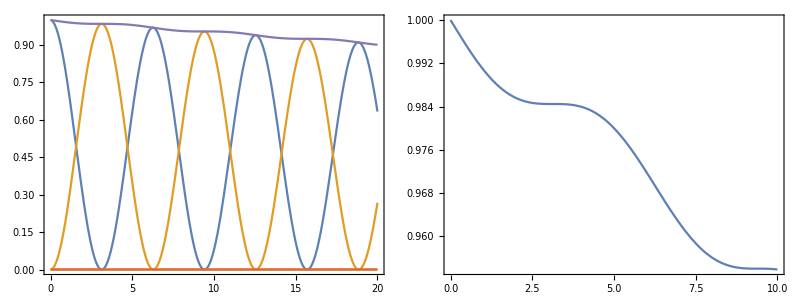

```mathematica
Grid[{
{
Plot[{p0mod["e","upm","e","upm"]/.ΩH->1/.γ->0.01,p0mod["g","upm","e","upm"]/.ΩH->1/.γ->0.01,p0mod["e","dwm","e","upm"]/.ΩH->1/.γ->0.01,p0mod["g","dwm","e","upm"]/.ΩH->1/.γ->0.01,p0totaleUp/.ΩH->1/.γ->0.01},{t,0,20}],

Plot[{p0totaleUp/.ΩH->1/.γ->0.01},{t,0,10}]
}
}]
```

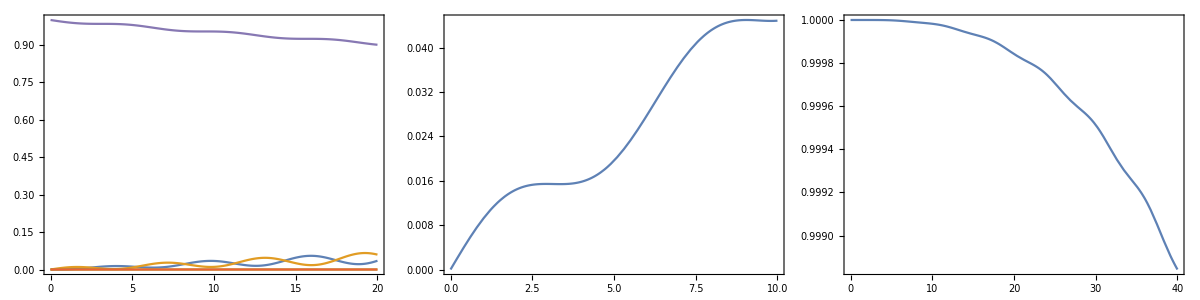

```mathematica
Grid[{
{
Plot[{p1Rmod["e","upm","e","upm"]/.ΩH->1/.γ->0.01,p1Rmod["g","upm","e","upm"]/.ΩH->1/.γ->0.01,p1Rmod["e","dwm","e","upm"]/.ΩH->1/.γ->0.01,p1Rmod["g","dwm","e","upm"]/.ΩH->1/.γ->0.01,p0totaleUp/.ΩH->1/.γ->0.01},{t,0,20}],

Plot[{p1RtotaleUp/.ΩH->1/.γ->0.01},{t,0,10}],

Plot[{(p0totaleUp+p1RtotaleUp+p1R1RtotaleUp)/.ΩH->1/.γ->0.01},{t,0,40}]
}
}]
```

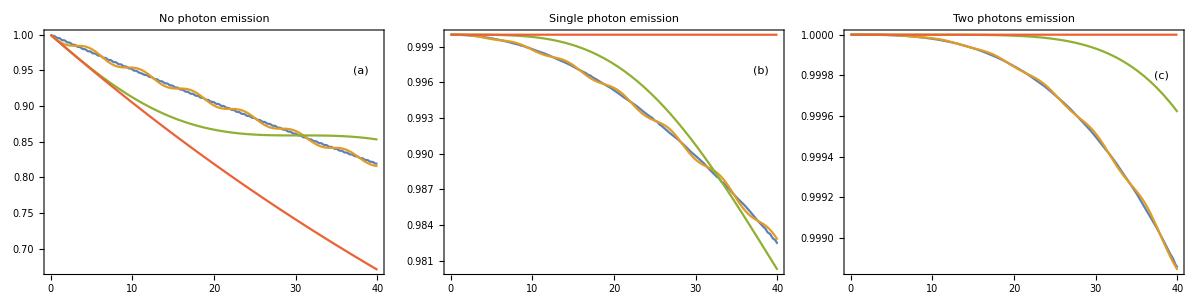

```mathematica
normalizationplots=Grid[{
{
Plot[
{(p0totaleUp)/.ΩH->10/.γ->0.01,
(p0totaleUp)/.ΩH->1/.γ->0.01,
(p0totaleUp)/.ΩH->0.1/.γ->0.01,
(p0totaleUp)/.ΩH->0.001/.γ-> 0.01},{t,0,40},
 PlotLabel->"No photon emission",
Epilog->Inset[alphabetlabel[[1]],{38,0.95}]],

Plot[
{(p0totaleUp+p1RtotaleUp)/.ΩH->10/.γ->0.01,
(p0totaleUp+p1RtotaleUp)/.ΩH->1/.γ->0.01,
(p0totaleUp+p1RtotaleUp)/.ΩH->0.1/.γ->0.01,
(p0totaleUp+p1RtotaleUp)/.ΩH->0.001/.γ->0.01},{t,0,40},
 PlotLabel->"Single photon emission",
Epilog->Inset[alphabetlabel[[2]],{38,0.997}]
],

Plot[
{(p0totaleUp+p1RtotaleUp+p1R1RtotaleUp)/.ΩH->10/.γ->0.01,
(p0totaleUp+p1RtotaleUp+p1R1RtotaleUp)/.ΩH->1/.γ->0.01,
(p0totaleUp+p1RtotaleUp+p1R1RtotaleUp)/.ΩH->0.1/.γ->0.01,
(p0totaleUp+p1RtotaleUp+p1R1RtotaleUp)/.ΩH->0.001/.γ->0.01},{t,0,40},
PlotRange->All,
 PlotLabel->"Two photons emission",
PlotLegends->legend[{MX@"\Omega_H=10",MX@"\Omega_H=1",MX@"\Omega_H=10^{-2}",MX@"\Omega_H= 10^{-3}"},{0.2,0.38}],
Epilog->Inset[alphabetlabel[[3]],{38,0.9998}]]
}
}]
Export[PlotsPath<>"NormalizationTruncationCheck.pdf",normalizationplots];
```

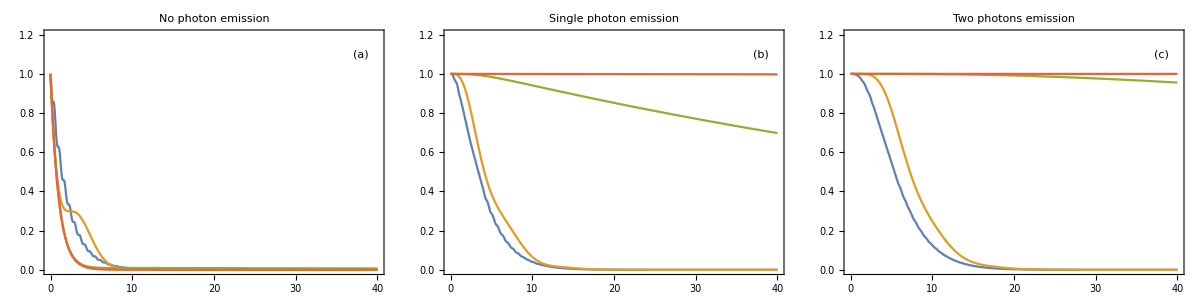

```mathematica
normalizationplots2=Grid[{
{
Plot[
{(p0totaleUp)/.ΩH->10/.γ->1,
(p0totaleUp)/.ΩH->1/.γ->1,
(p0totaleUp)/.ΩH->0.1/.γ->1,
(p0totaleUp)/.ΩH->8 0.001/.γ->1},{t,0,40},
PlotRange->{All,{0.,1.2}},
 PlotLabel->"No photon emission",
Epilog->Inset[alphabetlabel[[1]],{38,1.1}]],

Plot[
{(p0totaleUp+p1RtotaleUp)/.ΩH->10/.γ->1,
(p0totaleUp+p1RtotaleUp)/.ΩH->1/.γ->1,
(p0totaleUp+p1RtotaleUp)/.ΩH->0.1/.γ->1,
(p0totaleUp+p1RtotaleUp)/.ΩH->8 0.001/.γ->1},{t,0,40},
PlotRange->{All,{0.,1.2}},
 PlotLabel->"Single photon emission",
Epilog->Inset[alphabetlabel[[2]],{38,1.1}]
],

Plot[
{(p0totaleUp+p1RtotaleUp+p1R1RtotaleUp)/.ΩH->10/.γ->1,
(p0totaleUp+p1RtotaleUp+p1R1RtotaleUp)/.ΩH->1/.γ->1,
(p0totaleUp+p1RtotaleUp+p1R1RtotaleUp)/.ΩH->0.1/.γ->1,
(p0totaleUp+p1RtotaleUp+p1R1RtotaleUp)/.ΩH->8 0.001/.γ->1},{t,0,40},
PlotRange->{All,{0.,1.2}},
 PlotLabel->"Two photons emission",
PlotLegends->legend[{MX@"\Omega_H=10",MX@"\Omega_H=1",MX@"\Omega_H=10^{-2}",MX@"\Omega_H= 10^{-3}"},{0.8,0.38}],
Epilog->Inset[alphabetlabel[[3]],{38,1.1}]]
}
}]
Export[PlotsPath<>"NormalizationTruncationCheck2.pdf",normalizationplots2];
```

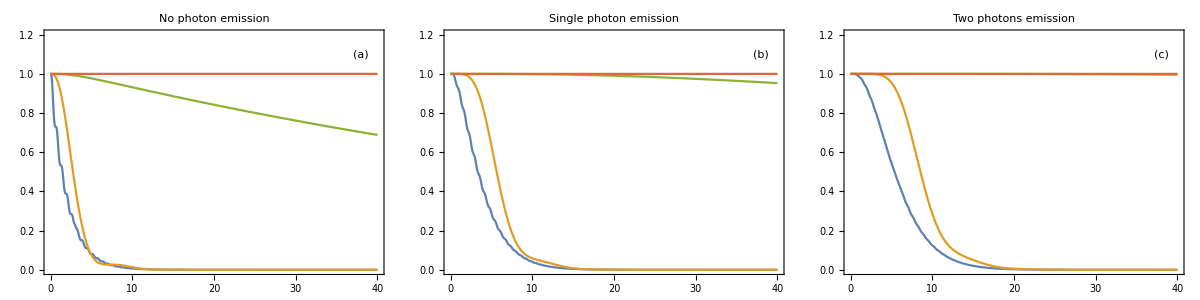

```mathematica
normalizationplot3=Grid[{
{
Plot[
{(p0totalgUp)/.ΩH->10/.γ->1,
(p0totalgUp)/.ΩH->1/.γ->1,
(p0totalgUp)/.ΩH->0.1/.γ->1,
(p0totalgUp)/.ΩH->0.001/.γ->1},{t,0,40},
PlotRange->{All,{0.,1.2}},
 PlotLabel->"No photon emission",
Epilog->Inset[alphabetlabel[[1]],{38,1.1}]],

Plot[
{(p0totalgUp+p1RtotalgUp)/.ΩH->10/.γ->1,
(p0totalgUp+p1RtotalgUp)/.ΩH->1/.γ->1,
(p0totalgUp+p1RtotalgUp)/.ΩH->0.1/.γ->1,
(p0totalgUp+p1RtotalgUp)/.ΩH->0.001/.γ->1},{t,0,40},
PlotRange->{All,{0.,1.2}},
 PlotLabel->"Single photon emission",
Epilog->Inset[alphabetlabel[[2]],{38,1.1}]
],

Plot[
{(p0totalgUp+p1RtotalgUp+p1R1RtotalgUp)/.ΩH->10/.γ->1,
(p0totalgUp+p1RtotalgUp+p1R1RtotalgUp)/.ΩH->1/.γ->1,
(p0totalgUp+p1RtotalgUp+p1R1RtotalgUp)/.ΩH->0.1/.γ->1,
(p0totalgUp+p1RtotalgUp+p1R1RtotalgUp)/.ΩH-> 0.001/.γ->1},{t,0,40},
PlotRange->{All,{0.,1.2}},
 PlotLabel->"Two photons emission",
PlotLegends->legend[{MX@"\Omega_H=10",MX@"\Omega_H=1",MX@"\Omega_H=10^{-2}",MX@"\Omega_H= 10^{-3}"},{0.8,0.38}],
Epilog->Inset[alphabetlabel[[3]],{38,1.1}]]
}
}]
Export[PlotsPath<>"NormalizationTruncationCheck2IntialStategUp.pdf",normalizationplot3];
```

### 5) Checking normalization for the simplified model: with spin precesion Ω ≥ 0 (Need to be done numerically)☑

In the last section we turned-off the spin precession Ω and checked the normalization of the driven wave-function truncated at two-photon component, in time for different values of Ω_H. There it was possible to compute the integrals symbolically. In this section I want to verify the same is true, yet for the simplified model adding the precession term. I tried to do it symbolically but it does not seems feasible due to the number of parameters. Hence, I’ll do the same numerically. The next step is check normalization for different Ω_g and Ω_e, i.e. for the real experimental parameters. This will provide us a solid ground to compute the quantities of interest for the experiment.

We have four parameters:
	1)Ω_H the drive,
	2) Ω the precession,
	3) The initial state ϵi,si, and
	4) The final state ϵf,sf

```mathematica
Exp2Ωprecessionlist
```

{0.,0.0771277,0.154255,0.231383,0.347074,0.385638,0.462766,0.694149}

```mathematica
Exp2Ωprecessionlist2={0.07712765957446809,0.15425531914893617};
drivingΩHlist = {10^-3,10^-1,1}//N;
```

```mathematica
PrettyTiming@Do[
PrintTemporary[Ωprecession];
PrintTemporary[Ωdriving];
p0simplifiedtable[ϵf,sf,ϵi,si,Ωprecession,Ωdriving]=Table[{τ,Abs[f0mod[ϵf,sf,ϵi,si,τ]/.γ->1/.ΩH->Ωdriving/.Ω->Ωprecession]^2},{τ,0,20,0.5}],
(*Since there was no emission, the fina state must be the excited one*)
{ϵf,{"e"}},
(*But it can start in any energy state*)
{ϵi,{"e","g"}},
(*With any spin*)
{sf,{"upm","dwm"}},
{si,{"upm","dwm"}},
{Ωprecession,Exp2Ωprecessionlist2},
{Ωdriving,drivingΩHlist}]
```

0h : 1m : 24s

```mathematica
DumpSave["p0simplifiedtable.mx",p0simplifiedtable];
```

```mathematica
Do[

p0simplifiedtableTotal["g","dwm",Exp2Ωprecessionlist[[l]],drivingΩHlist[[m]]]=Table[
{p0simplifiedtable["e","dwm","g","dwm",Exp2Ωprecessionlist[[l]],drivingΩHlist[[m]]][[i,1]],Sum[p0simplifiedtable[ϵf,sf,"g","dwm",Exp2Ωprecessionlist[[l]],drivingΩHlist[[m]]][[i,2]],{ϵf,{"e"}},{sf,{"upm","dwm"}}]},{i,1,Length@p0simplifiedtable["g","dwm","g","dwm",Exp2Ωprecessionlist[[1]],drivingΩHlist[[3]]]}],
{l,1,Length@Exp2Ωprecessionlist},
{m,1,Length@drivingΩHlist}
]
```

Part::partd: Part specification p0simplifiedtable[e,Dw,g,Dw,0.,0.001]⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification p0simplifiedtable[e,Up,g,Dw,0.,0.001]⟦1,2⟧ is longer than depth of object.

Part::partd: Part specification p0simplifiedtable[e,Dw,g,Dw,0.,0.001]⟦1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

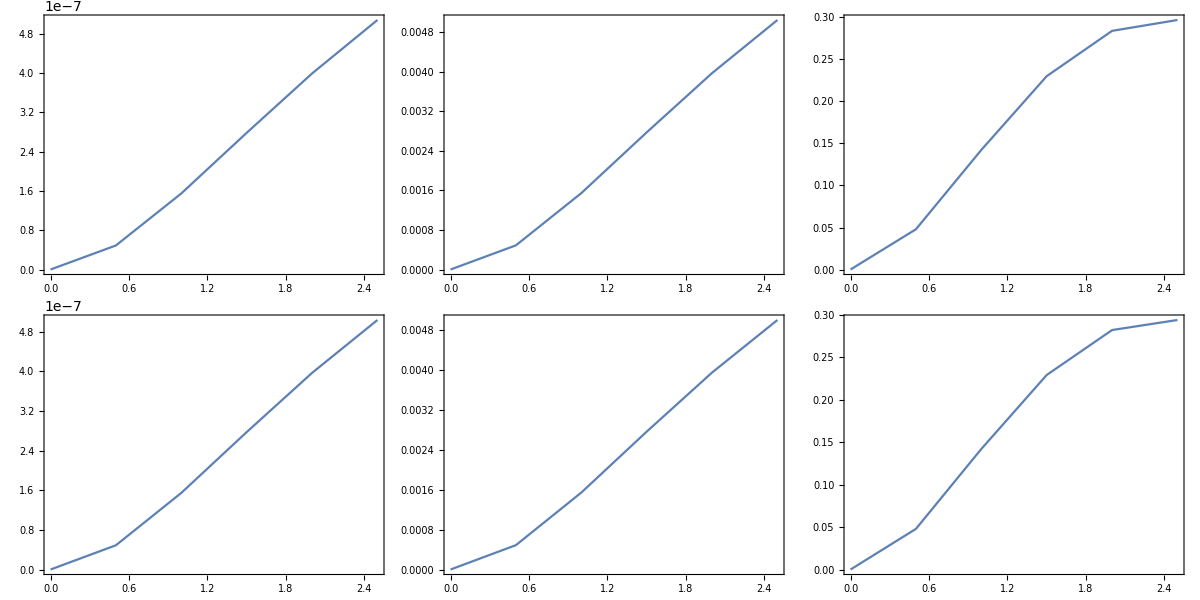

```mathematica
Grid[

Table[
ListLinePlot[
p0simplifiedtableTotal["g","dwm",Exp2Ωprecessionlist[[l]],drivingΩHlist[[m]]],PlotRange->All],
{l,1,Length@Exp2Ωprecessionlist},
{m,1,Length@drivingΩHlist}]



]
```

## 2. Fidelity of the spin at the moment of re-excitation

### 2.1 Time t = π/2Ωg=π/(2λΩ)

We set t = π/2Ωg=π/(2λΩ). The expression for the fidelity is given by:

```mathematica
fx = (1+(Ωe/γ)^2+(Ωg/γ)^2)/((1+4(ΔΩm/γ)^2)(1+4(ΔΩp/γ)^2))/.ΔΩm->(Ωg-Ωe)/2/.ΔΩp->(Ωg+Ωe)/2//cf(*ok*)
```

(γ^2 (γ^2+Ωe^2+Ωg^2))/((γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))

```mathematica
fyz = (1/(1+(Ωe/γ)^2)-(ΔΩm/γ)/(1+4(ΔΩm/γ)^2)-(ΔΩp/γ)/(1+4(ΔΩp/γ)^2))/.ΔΩm->(Ωg-Ωe)/2/.ΔΩp->(Ωg+Ωe)/2//cf(*ok*)
```

1/(1+Ωe^2/γ^2)-(γ Ωg (γ^2-Ωe^2+Ωg^2))/((γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))

```mathematica
ℱ = 1/2+nx/2 fx-(ny nz)/2 fyz//cf
```

1/4 (2+γ (-(2 ny nz γ)/(γ^2+Ωe^2)+(nx γ+ny nz (-Ωe+Ωg))/(γ^2+(Ωe-Ωg)^2)+(nx γ+ny nz (Ωe+Ωg))/(γ^2+(Ωe+Ωg)^2)))

```mathematica
ℱ=ℱ/.Ωe->Ω/.Ωg->λ Ω//cf
```

1/4 (2+γ (-(2 ny nz γ)/(γ^2+Ω^2)+(nx γ+ny nz (-1+λ) Ω)/(γ^2+(-1+λ)^2 Ω^2)+(nx γ+ny nz (1+λ) Ω)/(γ^2+(Ω+λ Ω)^2)))

Contour plot in the perfect situation x=(1,0,0), γ=1, the expression reduces to:

```mathematica
ℱλΩ=ℱ/.{nx->1,ny->0,nz->0,γ->1}//cf
```

1/4 (2+1/(1+(-1+λ)^2 Ω^2)+1/(1+(Ω+λ Ω)^2))

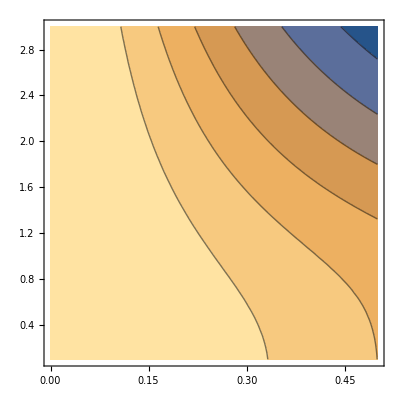

```mathematica
ContourPlot[ℱλΩ,{Ω,0.,0.5},{λ,0.1,3.}]
```

Super ideal situation marked with the dashed line, where λ=1:

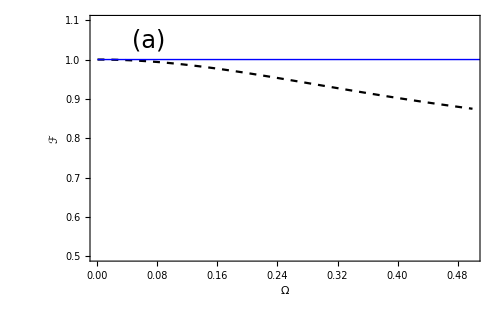

```mathematica
fig1a=Plot[ℱλΩ/.λ->1,{Ω,0.,0.5},
PlotRange->{All,{0.5,1.1}},

FrameLabel->{Style["Ω",FontFamily->"Times",FontSize->fontsize,Black],Style["ℱ",FontFamily->"Times",FontSize->fontsize,Black]},LabelStyle->Directive[FontFamily->"Times",FontSize->fontsize,Black],

PlotStyle->{Black,Dashed},

Epilog->{
{Text[Style["(a)",FontSize->fontsize,FontFamily->"Times",FontColor->Black],Scaled[{0.15,0.9}]]},(*Horizontal line*){Blue,Line[{{0,1},{1,1}}]}},

ImageSize->500]

Export[PlotsPath<>"fig1a.pdf",plot];
```

```mathematica
ℱλΩ
```

1/4 (2+1/(1+(-1+λ)^2 Ω^2)+1/(1+(Ω+λ Ω)^2))

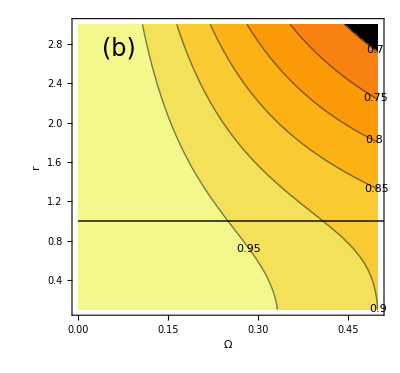

```mathematica
Module[{cf},
cf= MPLColorMap["Inferno"];
fig1b=
ContourPlot[ℱλΩ,{Ω,0.,0.5},{λ,0.1,3.},
AspectRatio->7/7.5,
PlotRange->All,

FrameLabel->{Style["Ω",FontFamily->"Times",FontSize->fontsize,Black],Style["r",FontFamily->"Times",FontSize->fontsize,Black]},
LabelStyle->Directive[FontFamily->"Times",FontSize->fontsize,Black],

ColorFunction->cf,
ContourLabels->All,
ColorFunctionScaling->False,

(*PlotLegends->Placed[BarLegend[{cf,{0,1}},LegendLabel->Style["ℱ",FontFamily->"Times",FontSize->fontsize,Black]],Right],
*)
Epilog->{
{Text[Style["(b)",FontSize->fontsize,FontFamily->"Times",FontColor->Black],Scaled[{0.15,0.9}]]},(*Horizontal line*){Line[{{0,1},{1,1}}]}},

ImageSize->400]
]
Export[overleafPath<>"fig1b.pdf",fig1b];
```

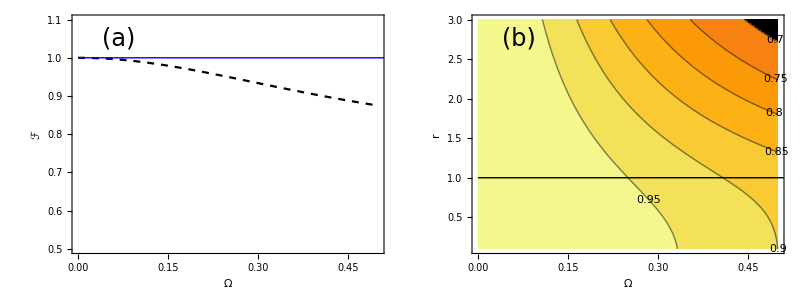

```mathematica
bothIdealscenariotg = Grid[{{fig1a,fig1b}}]
```